# Brandvain and Coop. Sperm dependent female meiotic drive.

## Model 1. Taditional female drive

## Set up

```mathematica
(*Allele and Genotype frequencies*)
ClearAll["Global`*"]
fA=1-fB;
fAA = fA^2+fA fB x;
fAB = 2fA fB(1-x);
fBB= fB^2+fA fB x;
```

### Drive

```mathematica
Subscript[fAA, Drive]=FullSimplify[fA(fAA+fAB (1-d))];
Subscript[fAB, Drive] =FullSimplify[fA(fBB+fAB d)+fB(fAA+fAB(1- d))];
Subscript[fBB, Drive] =FullSimplify[fB(fAB d+fBB )];
```

### Selection

```mathematica
wAA=1;wAB=1-hs;wBB=1-s; (*genotypic fitnesses*)
W̄=FullSimplify[Subscript[fAA, Drive] wAA+Subscript[fAB, Drive] wAB+Subscript[fBB, Drive] wBB];(*mean fitness*)
Subscript[fAA, Sel]=FullSimplify[(Subscript[fAA, Drive]*wAA)/W̄];
Subscript[fAB, Sel]=FullSimplify[(Subscript[fAB, Drive]*wAB)/W̄];
Subscript[fBB, Sel]=FullSimplify[(Subscript[fBB, Drive] wBB)/W̄];
Subscript[fA, Sel]=FullSimplify[Subscript[fAA, Sel]+Subscript[fAB, Sel]/2];
Subscript[fB, Sel]=FullSimplify[Subscript[fBB, Sel]+Subscript[fAB, Sel]/2];
ΔfA=FullSimplify[Subscript[fA, Sel]-fA];
ΔfB=FullSimplify[Subscript[fB, Sel]-fB];
```

## Analysis

For all analyses we assume HWE (i.e. x = 0), we relax this assumption in numerical iterations

### Invasion

```mathematica
scaledDeltaDriveWhenRare = (FullSimplify[ΔfB/(fB * (1-fB))/.x->0]/.fB->0)
```

1/2 (-1-2 d (-1+hs)-hs)

Noting that the change in frequency of a standard driver is independent of s when rare, we solve for the value of hs required for invasion.

```mathematica
invasionCrit=Solve[scaledDeltaDriveWhenRare ==0,hs]
```

{{hs→(-1+2 d)/(1+2 d)}}

### Fixation

```mathematica
scaledDeltaDriveWhenCommon=(FullSimplify[ΔfB/(fB * (1-fB))/.x->0]/.fB->1)
```

(1+hs+2 (d (-1+hs)-2 hs+s))/(2 (-1+s))

We solve for fixation conditions when recessive or not.

```mathematica
fixationCritRecessive=Solve[scaledDeltaDriveWhenCommon==0,s]/.hs->0
fixationCritNotRecessive=Solve[scaledDeltaDriveWhenCommon==0,s]
```

{{s→1/2 (-1+2 d)}}

{{s→1/2 (-1+2 d+3 hs-2 d hs)}}

### Equilibrium

We identify the equilibrium frequency of the standard driver

```mathematica
eqfB=Solve[(FullSimplify[(ΔfB/.x->0)])==0,fB][[4]]
```

{fB→(8 d hs-4 d s+√(-4 (1-2 d+hs+2 d hs) (-4 hs+8 d hs+2 s-4 d s)+(-8 d hs+4 d s)^2))/(2 (-4 hs+8 d hs+2 s-4 d s))}

We plot this equilibrium frequency assuming a recessive fitness cost.

```mathematica
ContourPlot[If[fB>1,1/0,If[fB<0,1/0,fB]]/.eqfB/.hs->0,{d,.5,1},{s,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"fB^*"],PlotLabel->"Equilibrium frequency of a standard driver with a recessive fitness cost",FrameLabel->{"d (drive of the B allele)","s (selection against driver, assuming recessive fitness cost)"}]
```

-Graphics-

```mathematica
FullSimplify[Subscript[fAA, Drive]+Subscript[fAB, Drive]+Subscript[fBB, Drive]]
```

1

## Model 2. Female drive depends on sperm haplotype (single pleitropic locus)

The B allele is transmited with probability, d, in heterozygous females when fertilized by B-bearing sperm. 
x represents the deviation from Hardy - Weinberg Equilibrium

## Setup

```mathematica
(*Allele and Genotype frequencies*)
ClearAll["Global`*"]
fA=1-fB;
fAA = fA^2+fA fB x;
fAB = 2fA fB(1-x);
fBB= fB^2+fA fB x;
```

#### Drive

```mathematica
(*Genotype frequencies after drive*)
Subscript[fAA, Drive]=FullSimplify[fA(fAA+fAB/2)];
Subscript[fAB, Drive] =FullSimplify[fB(fAA+fAB*(1-d))+fA(fAB/2+fBB)];
Subscript[fBB, Drive] =FullSimplify[fB(fAB d+fBB )];
```

#### Selection

```mathematica
wAA=1;wAB=1-hs;wBB=1-s; (*genotypic fitnesses*)
W̄=FullSimplify[Subscript[fAA, Drive] wAA+Subscript[fAB, Drive] wAB+Subscript[fBB, Drive] wBB];(*mean fitness*)
Subscript[fAA, Sel]=FullSimplify[(Subscript[fAA, Drive]*wAA)/W̄];
Subscript[fAB, Sel]=FullSimplify[(Subscript[fAB, Drive]*wAB)/W̄];
Subscript[fBB, Sel]=FullSimplify[(Subscript[fBB, Drive] wBB)/W̄];
Subscript[fA, Sel]=FullSimplify[Subscript[fAA, Sel]+Subscript[fAB, Sel]/2];
Subscript[fB, Sel]=FullSimplify[Subscript[fBB, Sel]+Subscript[fAB, Sel]/2];
ΔfA=FullSimplify[Subscript[fA, Sel]-fA];
ΔfB=FullSimplify[Subscript[fB, Sel]-fB];
```

## Analysis

Note, we assume no deviation from Hardy-Weinberg [i.e. x=0] for all analytical results, and therefore these answers are approximations. In the supplamentary material we show thats results of exact recursions are remarkably consistant from these approximate analystical solutions.

### Assuming the cost of drive is fully recessive [i.e. hs is zero]

#### Invasion

```mathematica
ΔfBinvade=(FullSimplify[ΔfB/.hs->0/.x->0]/fB^2/.fB->0)
```

1/2 (-1+d (2-4 s))

```mathematica
spermDepReceesiveInvade =Solve[ΔfBinvade==0,s]
```

{{s→(-1+2 d)/(4 d)}}

```mathematica
plotInvasion4spermDepRecessive=Plot[s/.spermDepReceesiveInvade [[1]],{d,.5,1},PlotStyle->{Black,Thick}];
```

```mathematica
plotRelChange4RarespermDepRecessive=ContourPlot[{ΔfBinvade},{d,0.5,1},{s,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"scaled ΔB"],FrameLabel->{"d (drive)","s (selection)"},PlotLabel->"Invasion of recessive sperm dependent driver"];
```

```mathematica
Show[plotRelChange4RarespermDepRecessive,plotInvasion4spermDepRecessive]
```

-Graphics-

#### Fixation

```mathematica
ΔfBfix=FullSimplify[FullSimplify[ΔfB/.hs->0/.x->0]/fA]/.fB->1
```

(-1+2 d-2 s)/(2-2 s)

```mathematica
spermDepReceesiveFix =Solve[ΔfBfix==0,s]
```

{{s→1/2 (-1+2 d)}}

```mathematica
(s/.spermDepReceesiveFix [[1]])
```

1/2 (-1+2 d)

```mathematica
plotFixation4spermDepRecessive=Plot[s/.spermDepReceesiveFix  [[1]],{d,.5,1},PlotStyle->{Red,Thick}];
```

```mathematica
(*Note we artificially rescaled z to be -.1 for all negative values*)
plotRelChange4CommonSpermDepRecessive=ContourPlot[If[s>(s/.spermDepReceesiveFix [[1]]),-.1,ΔfBfix],{d,0.5,1},{s,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"scaled ΔB"],FrameLabel->{"d (dirve)","s (selection)"},PlotLabel->"Fixation of recessive sperm dependent driver"];
```

```mathematica
Show[plotRelChange4CommonSpermDepRecessive,plotFixation4spermDepRecessive]
```

-Graphics-

#### Bistability Point

```mathematica
FBbistabSpermDepReceesive=Solve[FullSimplify[ΔfB/.hs->0/.x->0]==0,fB][[4]]
```

{fB→(1-2 d+4 d s)/(-2 s+4 d s)}

```mathematica
bistab=ContourPlot[(If[fB<0,0,If[fB>1,1,fB]])/.FBbistabSpermDepReceesive,{d,.5,1},{s,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"fB^*"],FrameLabel->{"d (dirve)","s (selection)"},PlotLabel->"Threshold frequency for fixation of recessive self-promoting driver"];
```

```mathematica
Show[bistab,plotFixation4spermDepRecessive,plotInvasion4spermDepRecessive]
```

-Graphics-

### Assuming the cost of drive is not fully recessive [i.e. hs is nonzero]

#### Invasion

Note  with any heterozgous cost (i.e. hs > 0) a self - promoting driver cannot invade

```mathematica
FullSimplify[FullSimplify[ΔfB/.x->0]/fB]/.fB->0
```

-hs

#### Fixation

```mathematica
ΔfBfix=FullSimplify[FullSimplify[FullSimplify[ΔfB/.x->0]/fA]/.fB->1]
```

(1+2 d (-1+hs)-3 hs+2 s)/(2 (-1+s))

```mathematica
spermDepNotReceesiveFix =Solve[ΔfBfix==0,s]
```

{{s→1/2 (-1+2 d+3 hs-2 d hs)}}

```mathematica
spermDepAddFix =Solve[ΔfBfix==0/.hs->s/2,s]
```

{{s→(2 (-1+2 d))/(1+2 d)}}

```mathematica
plotspermDepAddFix =Plot[s/.spermDepAddReceesiveFix ,{d,.5,1},PlotStyle->{Red,Thick}];
```

ReplaceAll::reps: {spermDepAddReceesiveFix} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

#### Bistability Point

```mathematica
FBbistabSpermDepNotReceesive=Solve[FullSimplify[ΔfB/.x->0]==0,fB][[3]]
```

{fB→(-1+2 d+3 hs+2 d hs-4 d s-√(-8 hs (-2 hs+4 d hs+2 s-4 d s)+(1-2 d-3 hs-2 d hs+4 d s)^2))/(2 (-2 hs+4 d hs+2 s-4 d s))}

An Example of a non - recessive driver [Assuming additivity]

```mathematica
bistab=ContourPlot[(If[fB<0,0,If[fB>1,1,fB]])/.FBbistabSpermDepNotReceesive/.hs->(s/2),{d,.5,1},{s,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"fB^*"],FrameLabel->{"d (dirve)","s (selection)"},PlotLabel->"Threshold frequency for fixation of recessive self-promoting driver"];
```

```mathematica
Show[bistab,plotspermDepAddFix]
```

-Graphics-

## Model 3. Female drive depends on male genotype (single pleitropic locus)

The B allele is transmited with probability, d and dh, in heterozygous females when fertilized BB and AB males, respectively.  
x represents the deviation from Hardy - Weinberg Equilibrium

## Setup

```mathematica
(*Allele and Genotype frequencies*)
ClearAll["Global`*"]
fA=1-fB;
fAA = fA^2+fA fB x;
fAB = 2fA fB(1-x);
fBB= fB^2+fA fB x;
```

### Drive

```mathematica
(*Genotype frequencies after drive*)
Subscript[fAA, Drive]=FullSimplify[fAA(fAA+fAB/2)+fAB(fAA/2+fAB(1-Subscript[d, het])/2)];
Subscript[fAB, Drive] =FullSimplify[fAA(fAB/2+fBB)+fAB(fAA/2+fAB/2+fBB(1-Subscript[d, hom]))+fBB(fAA+fAB/2)];
Subscript[fBB, Drive] =FullSimplify[fAB(fAB Subscript[d, het]/2+fBB Subscript[d, hom])+fBB(fAB/2+fBB)];
```

### Selection

```mathematica
wAA=1;wAB=1-hs;wBB=1-s; (*genotypic fitnesses*)
W̄=FullSimplify[Subscript[fAA, Drive] wAA+Subscript[fAB, Drive] wAB+Subscript[fBB, Drive] wBB];(*mean fitness*)
Subscript[fAA, Sel]=FullSimplify[(Subscript[fAA, Drive]*wAA)/W̄];
Subscript[fAB, Sel]=FullSimplify[(Subscript[fAB, Drive]*wAB)/W̄];
Subscript[fBB, Sel]=FullSimplify[(Subscript[fBB, Drive] wBB)/W̄];
Subscript[fA, Sel]=FullSimplify[Subscript[fAA, Sel]+Subscript[fAB, Sel]/2];
Subscript[fB, Sel]=FullSimplify[Subscript[fBB, Sel]+Subscript[fAB, Sel]/2];
ΔfA=FullSimplify[Subscript[fA, Sel]-fA];
ΔfB=FullSimplify[Subscript[fB, Sel]-fB];
```

```mathematica
FullSimplify[Subscript[fAA, Drive]+Subscript[fAB, Drive]+Subscript[fBB, Drive]]
```

1

## Analysis

### Analytical example - recessive fitness cost

#### Invasion

```mathematica
invasion4maleDepRecessive=Solve[((FullSimplify[(ΔfB/.x->0/.hs->0)]/fB^2)/.fB->0)==0,s]
```

{{s→(-1+2 d_het)/(2 d_het)}}

```mathematica
plotiInvasion4maleDepRecessive=Plot[s /. invasion4maleDepRecessive /. Subscript[d, het]-> Subscript[d, hom], {Subscript[d, hom], .5, 1}, PlotStyle -> {Black, Thick}];
```

#### Fixation

```mathematica
fixation4maleDepRecessive=Solve[(FullSimplify[(FullSimplify[(ΔfB/.x->0/.hs->0)/fA]/.fB->1)])==0,s]
```

{{s→1/2 (-1+2 d_hom)}}

```mathematica
plotFixation4maleDepRecessive=Plot[s /. fixation4maleDepRecessive /. Subscript[d, het] -> Subscript[d, hom], {Subscript[d, hom], .5, 1}, PlotStyle -> {Red, Thick}];
```

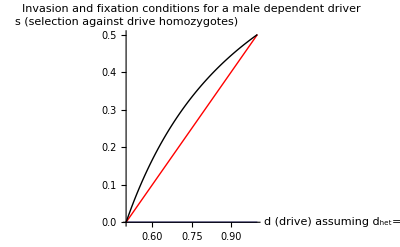

-Graphics-

```mathematica
Show[Plot[0,{Subscript[d, hom],0.5,1},AxesLabel->{"d (drive) assuming d_het=d_hom=d","s (selection against drive homozygotes)"},PlotRange->{{.5,1},{0,.5}}, PlotLabel->"Invasion and fixation conditions for a male dependent driver"],plotFixation4maleDepRecessive,plotiInvasion4maleDepRecessive]
```

#### Equlibrium

```mathematica
FBeqMaleepReceesive=Solve[FullSimplify[ΔfB/.x->0/.hs->0/.Subscript[d, het]->Subscript[d, hom]]==0,fB][[4]]
```

{fB→(2 (1-2 d_hom+2 s d_hom))/((-1+2 s) (-1+2 d_hom))}

```mathematica
eqfig=ContourPlot[ (If[fB<0,0,If[fB>1,1,fB]])/.FBeqMaleepReceesive,{Subscript[d, hom],0.5,1},{s,0,.5},PlotLegends->BarLegend[Automatic,LegendLabel->"fB^*"],FrameLabel->{"d (drive) assuming d_het=d_hom=d","s (selection, assuming recessive fitness cost)"}];
```

```mathematica
Show[eqfig,plotiInvasion4maleDepRecessive,plotFixation4maleDepRecessive]
```

-Graphics-

## Model 4. Female drive depends on sperm haplotype (two tightly linked, loci in coupling phase)

We have one locus with two alleles, A (non-driving) and B (traditional driver), as well as a tightly linked locus where one allele  modifies drive. Assuming no recombination this functions as a third allele, C. This tighly-linked locus is on the B background.
When C increases drive in heterozgous females it fertilizes, it is a drive enhancer (the B+ allele in our ms).
When C decreases drive in heterozgous females it fertilizes, it is a drive suppressor (the B- allele in our ms).

## Setup

```mathematica
ClearAll["Global`*"]
fA=.
fAA=.
fAB=.
fAC=.
fBB=.
fBC=.
fCC=.
minormod = {d1->d0+ϵ} (*assuming the sperm acting modifier additively increases drive by epsilon*);
SUMTOONE ={ fA->1-(fB+fC)};
HWE={fAA->fA^2,fAB->2fA fB,fAC->2fA fC,fBB -> fB^2, fBC->2fB fC,fCC->fC^2};
GENOFREQS = {fA->fAA+fAB/2+fAC/2,fB->fBB+fAB/2+fBC/2,fC->fCC+fBC/2+fBC/2};
```

### Drive

```mathematica
(*Here we caculate all genotypes after drive. For book-keeping purposes we distinguish between reciprocal homozygotes, but remove this distinction belowsum them below*)
```

```mathematica
AAn=FullSimplify[fAA*fAA*1+fAA*fAB*1/2+fAA*fAC*1/2+fAA*fBB*0+fAA*fBC*0+fAA*fCC*0+fAB*fAA*(1-d0)+fAB*fAB*(1-d0)/2+fAB*fAC*(1-d0)/2+fAB*fBB*0+fAB*fBC*0+fAB*fCC*0+fAC*fAA*(1-d0)+fAC*fAB*(1-d0)/2+fAC*fAC*(1-d0)/2+fAC*fBB*0+fAC*fBC*0+fAC*fCC*0+fBB*fAA*0+fBB*fAB*0+fBB*fAC*0+fBB*fBB*0+fBB*fBC*0+fBB*fCC*0+fBC*fAA*0+fBC*fAB*0+fBC*fAC*0+fBC*fBB*0+fBC*fBC*0+fBC*fCC*0+fCC*fAA*0+fCC*fAB*0+fCC*fAC*0+fCC*fBB*0+fCC*fBC*0+fCC*fCC*0+0];
ABn=FullSimplify[fAA*fAA*0+fAA*fAB*1/2+fAA*fAC*0+fAA*fBB*1+fAA*fBC*1/2+fAA*fCC*0+fAB*fAA*0+fAB*fAB*(1-d0)/2+fAB*fAC*0+fAB*fBB*(1-d0)+fAB*fBC*(1-d0)/2+fAB*fCC*0+fAC*fAA*0+fAC*fAB*(1-d0)/2+fAC*fAC*0+fAC*fBB*(1-d0)+fAC*fBC*(1-d0)/2+fAC*fCC*0+fBB*fAA*0+fBB*fAB*0+fBB*fAC*0+fBB*fBB*0+fBB*fBC*0+fBB*fCC*0+fBC*fAA*0+fBC*fAB*0+fBC*fAC*0+fBC*fBB*0+fBC*fBC*0+fBC*fCC*0+fCC*fAA*0+fCC*fAB*0+fCC*fAC*0+fCC*fBB*0+fCC*fBC*0+fCC*fCC*0+0];
ACn=FullSimplify[fAA*fAA*0+fAA*fAB*0+fAA*fAC*1/2+fAA*fBB*0+fAA*fBC*1/2+fAA*fCC*1+fAB*fAA*0+fAB*fAB*0+fAB*fAC*(1-d1)/2+fAB*fBB*0+fAB*fBC*(1-d1)/2+fAB*fCC*(1-d1)+fAC*fAA*0+fAC*fAB*0+fAC*fAC*(1-d1)/2+fAC*fBB*0+fAC*fBC*(1-d1)/2+fAC*fCC*(1-d1)+fBB*fAA*0+fBB*fAB*0+fBB*fAC*0+fBB*fBB*0+fBB*fBC*0+fBB*fCC*0+fBC*fAA*0+fBC*fAB*0+fBC*fAC*0+fBC*fBB*0+fBC*fBC*0+fBC*fCC*0+fCC*fAA*0+fCC*fAB*0+fCC*fAC*0+fCC*fBB*0+fCC*fBC*0+fCC*fCC*0+0];
BAn=FullSimplify[fAA*fAA*0+fAA*fAB*0+fAA*fAC*0+fAA*fBB*0+fAA*fBC*0+fAA*fCC*0+fAB*fAA*d0+fAB*fAB*d0/2+fAB*fAC*d0/2+fAB*fBB*0+fAB*fBC*0+fAB*fCC*0+fAC*fAA*0+fAC*fAB*0+fAC*fAC*0+fAC*fBB*0+fAC*fBC*0+fAC*fCC*0+fBB*fAA*1+fBB*fAB*1/2+fBB*fAC*1/2+fBB*fBB*0+fBB*fBC*0+fBB*fCC*0+fBC*fAA*1/2+fBC*fAB*1/4+fBC*fAC*1/4+fBC*fBB*0+fBC*fBC*0+fBC*fCC*0+fCC*fAA*0+fCC*fAB*0+fCC*fAC*0+fCC*fBB*0+fCC*fBC*0+fCC*fCC*0+0];
BBn=FullSimplify[fAA*fAA*0+fAA*fAB*0+fAA*fAC*0+fAA*fBB*0+fAA*fBC*0+fAA*fCC*0+fAB*fAA*0+fAB*fAB*d0/2+fAB*fAC*0+fAB*fBB*d0+fAB*fBC*d0/2+fAB*fCC*0+fAC*fAA*0+fAC*fAB*0+fAC*fAC*0+fAC*fBB*0+fAC*fBC*0+fAC*fCC*0+fBB*fAA*0+fBB*fAB*1/2+fBB*fAC*0+fBB*fBB*1+fBB*fBC*1/2+fBB*fCC*0+fBC*fAA*0+fBC*fAB*1/4+fBC*fAC*0+fBC*fBB*1/2+fBC*fBC*1/4+fBC*fCC*0+fCC*fAA*0+fCC*fAB*0+fCC*fAC*0+fCC*fBB*0+fCC*fBC*0+fCC*fCC*0+0];
BCn=FullSimplify[fAA*fAA*0+fAA*fAB*0+fAA*fAC*0+fAA*fBB*0+fAA*fBC*0+fAA*fCC*0+fAB*fAA*0+fAB*fAB*0+fAB*fAC*(d1)/2+fAB*fBB*0+fAB*fBC*(d1)/2+fAB*fCC*d1+fAC*fAA*0+fAC*fAB*0+fAC*fAC*0+fAC*fBB*0+fAC*fBC*0+fAC*fCC*0+fBB*fAA*0+fBB*fAB*0+fBB*fAC*1/2+fBB*fBB*0+fBB*fBC*1/2+fBB*fCC*1+fBC*fAA*0+fBC*fAB*0+fBC*fAC*1/4+fBC*fBB*0+fBC*fBC*1/4+fBC*fCC*1/2+fCC*fAA*0+fCC*fAB*0+fCC*fAC*0+fCC*fBB*0+fCC*fBC*0+fCC*fCC*0+0];
CAn=FullSimplify[fAA*fAA*0+fAA*fAB*0+fAA*fAC*0+fAA*fBB*0+fAA*fBC*0+fAA*fCC*0+fAB*fAA*0+fAB*fAB*0+fAB*fAC*0+fAB*fBB*0+fAB*fBC*0+fAB*fCC*0+fAC*fAA*d0+fAC*fAB*d0/2+fAC*fAC*d0/2+fAC*fBB*0+fAC*fBC*0+fAC*fCC*0+fBB*fAA*0+fBB*fAB*0+fBB*fAC*0+fBB*fBB*0+fBB*fBC*0+fBB*fCC*0+fBC*fAA*1/2+fBC*fAB*1/4+fBC*fAC*1/4+fBC*fBB*0+fBC*fBC*0+fBC*fCC*0+fCC*fAA*1+fCC*fAB*1/2+fCC*fAC*1/2+fCC*fBB*0+fCC*fBC*0+fCC*fCC*0+0];
CBn=FullSimplify[fAA*fAA*0+fAA*fAB*0+fAA*fAC*0+fAA*fBB*0+fAA*fBC*0+fAA*fCC*0+fAB*fAA*0+fAB*fAB*0+fAB*fAC*0+fAB*fBB*0+fAB*fBC*0+fAB*fCC*0+fAC*fAA*0+fAC*fAB*d0/2+fAC*fAC*0+fAC*fBB*d0+fAC*fBC*d0/2+fAC*fCC*0+fBB*fAA*0+fBB*fAB*0+fBB*fAC*0+fBB*fBB*0+fBB*fBC*0+fBB*fCC*0+fBC*fAA*0+fBC*fAB*1/4+fBC*fAC*0+fBC*fBB*1/2+fBC*fBC*1/4+fBC*fCC*0+fCC*fAA*0+fCC*fAB*1/2+fCC*fAC*0+fCC*fBB*1+fCC*fBC*1/2+fCC*fCC*0+0];
CCn=FullSimplify[fAA*fAA*0+fAA*fAB*0+fAA*fAC*0+fAA*fBB*0+fAA*fBC*0+fAA*fCC*0+fAB*fAA*0+fAB*fAB*0+fAB*fAC*0+fAB*fBB*0+fAB*fBC*0+fAB*fCC*0+fAC*fAA*0+fAC*fAB*0+fAC*fAC*d1/2+fAC*fBB*0+fAC*fBC*d1/2+fAC*fCC*d1+fBB*fAA*0+fBB*fAB*0+fBB*fAC*0+fBB*fBB*0+fBB*fBC*0+fBB*fCC*0+fBC*fAA*0+fBC*fAB*0+fBC*fAC*1/4+fBC*fBB*0+fBC*fBC*1/4+fBC*fCC*1/2+fCC*fAA*0+fCC*fAB*0+fCC*fAC*1/2+fCC*fBB*0+fCC*fBC*1/2+fCC*fCC*1+0];
```

```mathematica
(*Genotype frequencies after drive*)
Subscript[fAA, Drive] = FullSimplify[AAn];
Subscript[fAB, Drive] =FullSimplify[ABn+BAn];
Subscript[fAC, Drive]=FullSimplify[ACn+CAn];
Subscript[fBB, Drive]= FullSimplify[BBn];
Subscript[fBC, Drive]=FullSimplify[BCn+CBn];
Subscript[fCC, Drive]= FullSimplify[CCn];
(*check, do allele freqs sum to one?*)
FullSimplify[FullSimplify[Subscript[fAA, Drive] +Subscript[fAB, Drive] +Subscript[fAC, Drive]+Subscript[fBB, Drive]+Subscript[fBC, Drive]+Subscript[fCC, Drive]]/.HWE/.SUMTOONE]
```

1

### Selection

```mathematica
wAA=1;wAC=wAB=1-hs;wBB=wBC=wCC=1-s;
W̄= FullSimplify[(wAA  Subscript[fAA, Drive] +wAB Subscript[fAB, Drive]+wAC Subscript[fAC, Drive]+wBB Subscript[fBB, Drive]+wBC Subscript[fBC, Drive]+wCC Subscript[fCC, Drive])];
(*Because the C allele arises on the B background we assume it has the same impact on individual fitness*)
FullSimplify[W̄/.HWE/.SUMTOONE/.hs->0]
```

1+(fB+fC) (-2 d1 fC+2 d0 fB (-1+fB+fC)-(fB+fC) (fB+fC-2 d1 fC)) s

```mathematica
Subscript[fAA, Sel]= Subscript[fAA, Drive]  wAA/W̄;
Subscript[fAB, Sel]= Subscript[fAB, Drive] wAB/W̄;
Subscript[fAC, Sel]= Subscript[fAC, Drive] wAC /W̄;
Subscript[fBB, Sel]=Subscript[fBB, Drive] wBB/W̄;
Subscript[fBC, Sel]=Subscript[fBC, Drive] wBC/W̄;
Subscript[fCC, Sel]=Subscript[fCC, Drive] wCC/W̄;
Subscript[fA, Sel]=FullSimplify[Subscript[fAA, Sel]+(Subscript[fAB, Sel]+Subscript[fAC, Sel])/2];
Subscript[fB, Sel]=FullSimplify[Subscript[fBB, Sel]+(Subscript[fAB, Sel]+Subscript[fBC, Sel])/2];
Subscript[fC, Sel]=FullSimplify[Subscript[fCC, Sel]+(Subscript[fAC, Sel]+Subscript[fBC, Sel])/2];
ΔfA=FullSimplify[Subscript[fA, Sel]-fA];
ΔfB=FullSimplify[Subscript[fB, Sel]-fB];
ΔfC=FullSimplify[Subscript[fC, Sel]-fC];

(*Check: do genotype freqs after selection sum to one?*)
FullSimplify[Subscript[fA, Sel]+Subscript[fB, Sel]+Subscript[fC, Sel]]
```

1

## Analysis

#### Analysis - a standard driver [i.e. C is absent]

Note, we assume no deviation from Hardy - Weinberg for all analytical results, and therefore these answers are approximations. In the supplamentary material we show thats results of exact recursions are remarkably consistant from these approximate analystical solutions.

Invasion of standard driver - note the driver always invades when it has a recessive fitness cost. Reassuringly, this reproduces model 1.

```mathematica
invasionStandardDriver=Solve[(FullSimplify[(ΔfB/.GENOFREQS/.HWE/.SUMTOONE/.fC->0)/fB]/.fB->0)==0,hs]
```

{{hs→(-1+2 d0)/(1+2 d0)}}

Fixation of standard driver

```mathematica
fixationStandardDriver=Solve[(FullSimplify[(ΔfB/fA/.GENOFREQS/.HWE/.SUMTOONE/.fC->0)]/.fB->1)==0,s]
```

{{s→1/2 (-1+2 d0+3 hs-2 d0 hs)}}

```mathematica
(*fixation of a standard recessive driver*)
fixationStandardDriver/.hs->0
```

{{s→1/2 (-1+2 d0)}}

Equilibrium

```mathematica
(*Equilibrium frequency of a standard driver]*)
```

```mathematica
eqfB=Solve[(ΔfB/.GENOFREQS/.HWE/.SUMTOONE/.fC->0)==0,fB][[4]]
```

{fB→(8 d0 hs-4 d0 s+√(-4 (1-2 d0+hs+2 d0 hs) (-4 hs+8 d0 hs+2 s-4 d0 s)+(-8 d0 hs+4 d0 s)^2))/(2 (-4 hs+8 d0 hs+2 s-4 d0 s))}

```mathematica
(*Plot of equilibrium frequency of standard driver assuming full recessivity*)
```

```mathematica
ContourPlot[If[fB>1,1/0,If[fB<0,1/0,fB]]/.eqfB/.hs->0,{d0,.5,1},{s,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"fB^*"],PlotLabel->"Equilibrium frequency of a standard driver with a recessive fitness cost",FrameLabel->{"d0 (drive of the B allele)","s (selection against driver, assuming recessive fitness cost)"}]
```

-Graphics-

#### Invasion of sperm acting drive modifier tighly linked with the driver, and on the driving background

```mathematica
(*change in frequency of the drive modifier when rare and when alleles at the drive locus are in drive-viability equilibrium, mutliplied by Wbar/fC [this value is always positive and will not influence the sign]*)
wbarDeltaSpermDrive=FullSimplify[FullSimplify[W̄ ΔfC/(fC)/.HWE/.SUMTOONE]/.fC->0/.eqfB/.minormod]
```

((hs-s) (-1-hs-√2 √((1+hs-2 d0 (2+d0 (-2+s))) (2 hs-s))+2 d0 (2 (-1+d0) (-1+hs)+s)) ϵ)/(2 (1-2 d0)^2 (2 hs-s))

```mathematica
(*Plotting change this change in frequency when the sperm acting locus is rare, increases drive, and when the fitness cost of drive is fully recessive. NOTE: This sperm enhancer of drive cannot invade*)
```

```mathematica
ContourPlot[If[fB>1,1/0,If[fB<0.0001,0,wbarDeltaSpermDrive]]/.eqfB/.ϵ->0.01/.hs->0,{d0,0.5,1},{s,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"scaled ΔB^+"],PlotLabel->"A sperm-acting drive enhancer (the B^+ haplotype) cannot invade\n(assuming a recessive fitness cost of drive)",FrameLabel->{"d0 (drive of the B allele)","s (selection against driver, assuming recessive fitness cost)"}]
```

Greater::nord: Invalid comparison with 7.49301  - 83.3298\ ⅈ attempted.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^1. encountered.

Greater::nord: Invalid comparison with 3.99825  - 83.5704\ ⅈ attempted.

General::stop: Further output of Greater :: nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

-Graphics-

```mathematica
(*Plotting change this change in frequency when the sperm acting locus is rare and decreases drive, and when the fitness cost of drive is fully recessive. NOTE: This sperm suppresor always invades*)
```

```mathematica
ContourPlot[If[fB>1,1/0,If[fB<0.0001,0,wbarDeltaSpermDrive]]/.eqfB/.ϵ->-0.01/.hs->0,{d0,0.5,1},{s,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"scaled ΔB^-"],PlotLabel->"A sperm-acting drive suppressor (the B^- haplotype) always invades\n(assuming a recessive fitness cost of drive)",FrameLabel->{"d0 (drive of the B allele)","s (selection against driver, assuming recessive fitness cost)"}]
```

Greater::nord: Invalid comparison with 7.49301  - 83.3298\ ⅈ attempted.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^1. encountered.

Greater::nord: Invalid comparison with 3.99825  - 83.5704\ ⅈ attempted.

General::stop: Further output of Greater :: nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

-Graphics-

```mathematica
(*Plotting change this change in frequency when hte extent of drive is mild [d0 = .6] and the sperm acting locus is rare and increase drive. NOTE: This sperm enhancer never invades*)
ContourPlot[(If[fB>1,1/0,If[fB<0.0000001,0,wbarDeltaSpermDrive]]/.eqfB/.ϵ->0.01/.d0->.6),{s,0,1},{hs,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"scaled ΔB^+"],PlotLabel->"A sperm-acting drive enhancer (the B^+ haplotype) cannot invade\n(assuming drive-selection equilibrium of a modest driver, d0 = .6)",FrameLabel->{"s (selection against drive homozygotes)","hs (selection against drive heterozygotes)"}]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with 3.  + 63.2179\ ⅈ attempted.

-Graphics-

```mathematica
(*Plotting change this change in frequency when hte extent of drive is mild [d0 = .98] and the sperm acting locus is rare and increase drive. NOTE: This sperm enhancer never invades*)ContourPlot[(If[fB>1,1/0,If[fB<=0.001,-0.000000001,wbarDeltaSpermDrive]]/.eqfB/.ϵ->0.01/.d0->.98),{s,0,1},{hs,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"scaled ΔB^+"],PlotLabel->"A sperm-acting drive enhancer (the B^+ haplotype) cannot invade\n(assuming drive-selection equilibrium of a strong driver, d0 = .98)",FrameLabel->{"s (selection against drive homozygotes)","hs (selection against drive heterozygotes)"}]
```

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with 1.02083  - 2.442\ ⅈ attempted.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^1. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with 1.02083  - 1.56808\ ⅈ attempted.

General::stop: Further output of Greater :: nord will be suppressed during this calculation.

-Graphics-

-Graphics-

-Graphics-

#### Replacement of traditional driver by sperm acting drive suppressor tighly linked with the driver, and on the driving background

Equilibrium frequency of drive suppresor

```mathematica
eqfC=Solve[(FullSimplify[ΔfC/.HWE/.SUMTOONE/.minormod/.fB->0])==0,fC][[4]];
```

```mathematica
(*Equilibrium frequency of a linked, coupled, drive suppressor when the fitness costs of drive are recessive*)
```

```mathematica
ContourPlot[If[fC<1&&fC>0,(fC),1/0]/. eqfC/.hs->0/.ϵ->-.001,{d0,.5,1},{s,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"fB^(-  *)"],PlotLabel->"Equlibrium freq. of sperm-acting drive suppressor (the B^- haplotype)\n(assuming an initial complete driver, d0 = 1)",FrameLabel->{"d0 (drive of the B allele)","s (selection against drive homozygotes)"}]
```

-Graphics-

```mathematica
(*Equilibrium frequency of a linked, coupled, drive suppressor when drive is complete*)
```

```mathematica
ContourPlot[If[fC<1&&fC>0,(fC),1/0]/. eqfC/.hs->0/.ϵ->-.001/.d0->1,{s,0,1},{hs,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"fB^(-  *)"],PlotLabel->"Equlibrium freq. of a sperm-acting drive suppressor (the B^- haplotype) \n(assuming an initial complete driver, d0 = 1)",FrameLabel->{"s (selection against drive homozygotes)","hs (selection against drive heterozygotes)"}]
```

Power::infy: Infinite expression 1/0 encountered.

Less::nord: Invalid comparison with 1.00802  - 2.45019\ ⅈ attempted.

Greater::nord: Invalid comparison with 1.00802  - 2.45019\ ⅈ attempted.

Less::nord: Invalid comparison with 1.00802  - 2.45019\ ⅈ attempted.

Greater::nord: Invalid comparison with 1.00802  - 2.45019\ ⅈ attempted.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^1. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Less::nord: Invalid comparison with 1.00451  - 1.58082\ ⅈ attempted.

General::stop: Further output of Less :: nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with 1.00451  - 1.58082\ ⅈ attempted.

General::stop: Further output of Greater :: nord will be suppressed during this calculation.

-Graphics-

Equilibrium frequency of drive/sperm  acting  suppresor haplotype is often less than that of the standard driver it replaces.

```mathematica
(*Differecce in equilibrium frequency of the B- and B haplotypes*)
ContourPlot[If[fC<1&&fB<1&&fC>0&&fB>0,(fC-fB),1/0]/.eqfB/. eqfC/.hs->0/.ϵ->-.001,{d0,.5,1},{s,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"fB^(-  *) - fB^*"],PlotLabel->"Difference in equlibrium frequency of a drive suppresor (B^- haplotype)\n and the driver it replaces (assuming a recessive cost of the drive allele)",FrameLabel->{"d0 (drive of the B allele)","s (selection against drive homozygotes)"}]
```

-Graphics-

```mathematica
ContourPlot[If[fC<1&&fB<1&&fC>0&&fB>0,(fC-fB),1/0]/.eqfB/. eqfC/.hs->(s/4)/.ϵ->-.001,{d0,.5,1},{s,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"fB^(-  *) - fB^*"],PlotLabel->"Difference in equlibrium frequency of a drive suppresor (B^- haplotype)\n and the driver it replaces (assuming a heterozygote cost, hs = s/4)",FrameLabel->{"d0 (drive of the B allele)","s (selection against drive homozygotes)"}]
```

-Graphics-

```mathematica
(*change in frequency of a rare traditional driver when the drive-sperm suppressor haplotype and the ondriving hplotype are at drive selection equilibrium, mutliplied by Wbar/fC [this value is always positive and will not influence the sign]*)
wbarDeltaTradDrive=FullSimplify[FullSimplify[W̄ ΔfB/(fB)/.HWE/.SUMTOONE]/.fB->0/.eqfC/.minormod];
```

```mathematica
(*Plotting the change in frequency of a rare traditional driving haplotype when the sperm drive suppresor is at drive selection balance. ASSUMING the fitness cost of drive is fully recessive. NOTE: This sperm enhancer of drive cannot invade*)
```

```mathematica
ContourPlot[If[fC>1,1/0,If[fC<0.0001,0,wbarDeltaTradDrive]]/.eqfC/.ϵ->-0.001/.hs->0,{d0,0.5,1},{s,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"scaled ΔB"],PlotLabel->"A fixed drive suppresor (B^- haplotype) cannot be displaced by \n a traditional driver (assuming a recessive fitness cost of drive)",
FrameLabel->{"d0 (drive of the B allele)","s (selection against driver, assuming recessive fitness cost)"}]
```

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with 53.7184  - 64.9128\ ⅈ attempted.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^1. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

-Graphics-

```mathematica
(*Plotting the change in frequency of a rare traditional driving haplotype when the sperm drive suppresor is at drive selection balance. ASSUMING a fitness cost of drive in homozygotes (hs->s/4). NOTE: This sperm enhancer of drive cannot invade*)
```

```mathematica
ContourPlot[If[fC>1,1/0,If[fC<0.0001,0,wbarDeltaTradDrive]]/.eqfC/.ϵ->-0.001/.hs->s/4,{d0,0.5,1},{s,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"scaled ΔB"],PlotLabel->"A fixed sperm-acting drive suppresor cannot be displaced by a traditional \n(assuming a recessive fitness cost of drive)",FrameLabel->{"d0 (drive of the B allele)","s (selection against driver, assuming recessive fitness cost)"}]
```

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with 104.123  - 58.7778\ ⅈ attempted.

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0.^1. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Greater::nord: Invalid comparison with 69.1031  - 97.0611\ ⅈ attempted.

General::stop: Further output of Greater :: nord will be suppressed during this calculation.

```mathematica
ContourPlot[If[fC>1,1/0,If[fC<0.0001,0,wbarDeltaTradDrive]]/.eqfC/.ϵ->-0.001/.d0->1,{s,0,1},{hs,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"scaled ΔB"],PlotLabel->"A fixed sperm-acting drive suppresor cannot be displaced by a traditional \n(assuming perfect drive)",FrameLabel->{"s (selection against drive homozygotes)","hs (selection against drive heterozygotes)"}]
```

-Graphics-

```mathematica
￼
```

## Model 5. Female drive depends on sperm haplotype (two tightly linked, loci in repulsion phase)

We have one locus with two alleles, A (non-driving) and B (traditional driver), as well as a tightly linked locus where one allele modifies drive. This tighly-linked locus is on the A background. Assuming no recombination this functions as a third allele, C. 
When C increases drive in heterozgous females it fertilizes, it is a drive enhancer (the A+ allele [not discussed in our ms]).
When C decreases drive in heterozgous females it fertilizes, it is a drive suppressor (the A- allele in our ms).

## Setup

```mathematica
ClearAll["Global`*"]
fA=.
fAA=.
fAB=.
fAC=.
fBB=.
fBC=.
fCC=.
minormod = {d1->d0+ϵ} (*assuming the sperm acting modifier additively increases drive by epsilon*);
SUMTOONE ={ fA->1-(fB+fC)};
HWE={fAA->fA^2,fAB->2fA fB,fAC->2fA fC,fBB -> fB^2, fBC->2fB fC,fCC->fC^2};
GENOFREQS = {fA->fAA+fAB/2+fAC/2,fB->fBB+fAB/2+fBC/2,fC->fCC+fBC/2+fBC/2};
```

## Drive

```mathematica
(*Here we caculate all genotypes after drive. For book-keeping purposes we distinguish between reciprocal homozygotes, but remove this distinction belowsum them below*)
```

```mathematica
AAn=FullSimplify[fAA*fAA*1+fAA*fAB*1/2+fAA*fAC*1/2+fAA*fBB*0+fAA*fBC*0+fAA*fCC*0+fAB*fAA*(1-d0)+fAB*fAB*(1-d0)/2+fAB*fAC*(1-d0)/2+fAB*fBB*0+fAB*fBC*0+fAB*fCC*0+fAC*fAA*1/2+fAC*fAB*1/4+fAC*fAC*1/4+fAC*fBB*0+fAC*fBC*0+fAC*fCC*0+fBB*fAA*0+fBB*fAB*0+fBB*fAC*0+fBB*fBB*0+fBB*fBC*0+fBB*fCC*0+fBC*fAA*0+fBC*fAB*0+fBC*fAC*0+fBC*fBB*0+fBC*fBC*0+fBC*fCC*0+fCC*fAA*0+fCC*fAB*0+fCC*fAC*0+fCC*fBB*0+fCC*fBC*0+fCC*fCC*0+0];
ABn=FullSimplify[fAA*fAA*0+fAA*fAB*1/2+fAA*fAC*0+fAA*fBB*1+fAA*fBC*1/2+fAA*fCC*0+fAB*fAA*0+fAB*fAB*(1-d0)/2+fAB*fAC*0+fAB*fBB*(1-d0)+fAB*fBC*(1-d0)/2+fAB*fCC*0+fAC*fAA*0+fAC*fAB*1/4+fAC*fAC*0+fAC*fBB*1/2+fAC*fBC*1/4+fAC*fCC*0+fBB*fAA*0+fBB*fAB*0+fBB*fAC*0+fBB*fBB*0+fBB*fBC*0+fBB*fCC*0+fBC*fAA*0+fBC*fAB*0+fBC*fAC*0+fBC*fBB*0+fBC*fBC*0+fBC*fCC*0+fCC*fAA*0+fCC*fAB*0+fCC*fAC*0+fCC*fBB*0+fCC*fBC*0+fCC*fCC*0+0];
ACn=FullSimplify[fAA*fAA*0+fAA*fAB*0+fAA*fAC*1/2+fAA*fBB*0+fAA*fBC*1/2+fAA*fCC*1+fAB*fAA*0+fAB*fAB*0+fAB*fAC*(1-d1)/2+fAB*fBB*0+fAB*fBC*(1-d1)/2+fAB*fCC*(1-d1)+fAC*fAA*0+fAC*fAB*0+fAC*fAC*1/4+fAC*fBB*0+fAC*fBC*1/4+fAC*fCC*1/2+fBB*fAA*0+fBB*fAB*0+fBB*fAC*0+fBB*fBB*0+fBB*fBC*0+fBB*fCC*0+fBC*fAA*0+fBC*fAB*0+fBC*fAC*0+fBC*fBB*0+fBC*fBC*0+fBC*fCC*0+fCC*fAA*0+fCC*fAB*0+fCC*fAC*0+fCC*fBB*0+fCC*fBC*0+fCC*fCC*0+0];
BAn=FullSimplify[fAA*fAA*0+fAA*fAB*0+fAA*fAC*0+fAA*fBB*0+fAA*fBC*0+fAA*fCC*0+fAB*fAA*d0+fAB*fAB*d0/2+fAB*fAC*d0/2+fAB*fBB*0+fAB*fBC*0+fAB*fCC*0+fAC*fAA*0+fAC*fAB*0+fAC*fAC*0+fAC*fBB*0+fAC*fBC*0+fAC*fCC*0+fBB*fAA*1+fBB*fAB*1/2+fBB*fAC*1/2+fBB*fBB*0+fBB*fBC*0+fBB*fCC*0+fBC*fAA*d0+fBC*fAB*d0/2+fBC*fAC*(d0)/2+fBC*fBB*0+fBC*fBC*0+fBC*fCC*0+fCC*fAA*0+fCC*fAB*0+fCC*fAC*0+fCC*fBB*0+fCC*fBC*0+fCC*fCC*0+0];
BBn=FullSimplify[fAA*fAA*0+fAA*fAB*0+fAA*fAC*0+fAA*fBB*0+fAA*fBC*0+fAA*fCC*0+fAB*fAA*0+fAB*fAB*d0/2+fAB*fAC*0+fAB*fBB*d0+fAB*fBC*d0/2+fAB*fCC*0+fAC*fAA*0+fAC*fAB*0+fAC*fAC*0+fAC*fBB*0+fAC*fBC*0+fAC*fCC*0+fBB*fAA*0+fBB*fAB*1/2+fBB*fAC*0+fBB*fBB*1+fBB*fBC*1/2+fBB*fCC*0+fBC*fAA*0+fBC*fAB*d0/2+fBC*fAC*0+fBC*fBB*d0+fBC*fBC*(d0)/2+fBC*fCC*0+fCC*fAA*0+fCC*fAB*0+fCC*fAC*0+fCC*fBB*0+fCC*fBC*0+fCC*fCC*0+0];
BCn=FullSimplify[fAA*fAA*0+fAA*fAB*0+fAA*fAC*0+fAA*fBB*0+fAA*fBC*0+fAA*fCC*0+fAB*fAA*0+fAB*fAB*0+fAB*fAC*(d1)/2+fAB*fBB*0+fAB*fBC*(d1)/2+fAB*fCC*d1+fAC*fAA*0+fAC*fAB*0+fAC*fAC*0+fAC*fBB*0+fAC*fBC*0+fAC*fCC*0+fBB*fAA*0+fBB*fAB*0+fBB*fAC*1/2+fBB*fBB*0+fBB*fBC*1/2+fBB*fCC*1+fBC*fAA*0+fBC*fAB*0+fBC*fAC*(d1)/2+fBC*fBB*0+fBC*fBC*(d1)/2+fBC*fCC*d1+fCC*fAA*0+fCC*fAB*0+fCC*fAC*0+fCC*fBB*0+fCC*fBC*0+fCC*fCC*0+0];
CAn=FullSimplify[fAA*fAA*0+fAA*fAB*0+fAA*fAC*0+fAA*fBB*0+fAA*fBC*0+fAA*fCC*0+fAB*fAA*0+fAB*fAB*0+fAB*fAC*0+fAB*fBB*0+fAB*fBC*0+fAB*fCC*0+fAC*fAA*1/2+fAC*fAB*1/4+fAC*fAC*1/4+fAC*fBB*0+fAC*fBC*0+fAC*fCC*0+fBB*fAA*0+fBB*fAB*0+fBB*fAC*0+fBB*fBB*0+fBB*fBC*0+fBB*fCC*0+fBC*fAA*(1-d0)+fBC*fAB*(1-d0)/2+fBC*fAC*(1-d0)/2+fBC*fBB*0+fBC*fBC*0+fBC*fCC*0+fCC*fAA*1+fCC*fAB*1/2+fCC*fAC*1/2+fCC*fBB*0+fCC*fBC*0+fCC*fCC*0+0];
CBn=FullSimplify[fAA*fAA*0+fAA*fAB*0+fAA*fAC*0+fAA*fBB*0+fAA*fBC*0+fAA*fCC*0+fAB*fAA*0+fAB*fAB*0+fAB*fAC*0+fAB*fBB*0+fAB*fBC*0+fAB*fCC*0+fAC*fAA*0+fAC*fAB*1/4+fAC*fAC*0+fAC*fBB*1/2+fAC*fBC*1/4+fAC*fCC*0+fBB*fAA*0+fBB*fAB*0+fBB*fAC*0+fBB*fBB*0+fBB*fBC*0+fBB*fCC*0+fBC*fAA*0+fBC*fAB*(1-d0)/2+fBC*fAC*0+fBC*fBB*(1-d0)+fBC*fBC*(1-d0)/2+fBC*fCC*0+fCC*fAA*0+fCC*fAB*1/2+fCC*fAC*0+fCC*fBB*1+fCC*fBC*1/2+fCC*fCC*0+0];
CCn=FullSimplify[fAA*fAA*0+fAA*fAB*0+fAA*fAC*0+fAA*fBB*0+fAA*fBC*0+fAA*fCC*0+fAB*fAA*0+fAB*fAB*0+fAB*fAC*0+fAB*fBB*0+fAB*fBC*0+fAB*fCC*0+fAC*fAA*0+fAC*fAB*0+fAC*fAC*1/4+fAC*fBB*0+fAC*fBC*1/4+fAC*fCC*1/2+fBB*fAA*0+fBB*fAB*0+fBB*fAC*0+fBB*fBB*0+fBB*fBC*0+fBB*fCC*0+fBC*fAA*0+fBC*fAB*0+fBC*fAC*(1-d1)/2+fBC*fBB*0+fBC*fBC*(1-d1)/2+fBC*fCC*(1-d1)+fCC*fAA*0+fCC*fAB*0+fCC*fAC*1/2+fCC*fBB*0+fCC*fBC*1/2+fCC*fCC*1+0];
```

```mathematica
(*Genotype frequencies after drive*)
Subscript[fAA, Drive] = FullSimplify[AAn];
Subscript[fAB, Drive] =FullSimplify[ABn+BAn];
Subscript[fAC, Drive]=FullSimplify[ACn+CAn];
Subscript[fBB, Drive]= FullSimplify[BBn];
Subscript[fBC, Drive]=FullSimplify[BCn+CBn];
Subscript[fCC, Drive]= FullSimplify[CCn];
(*check, do allele freqs sum to one?*)
FullSimplify[FullSimplify[Subscript[fAA, Drive] +Subscript[fAB, Drive] +Subscript[fAC, Drive]+Subscript[fBB, Drive]+Subscript[fBC, Drive]+Subscript[fCC, Drive]]/.HWE/.SUMTOONE]
```

1

## Selection

```mathematica
wAA=wAC=wCC=1;wAB=wBC=1-hs;wBB=1-s;
W̄= FullSimplify[(wAA  Subscript[fAA, Drive] +wAB Subscript[fAB, Drive]+wAC Subscript[fAC, Drive]+wBB Subscript[fBB, Drive]+wBC Subscript[fBC, Drive]+wCC Subscript[fCC, Drive])];
(*Because the C allele arises on the B background we assume it has the same impact on individual fitness*)
FullSimplify[W̄/.HWE/.SUMTOONE/.hs->0]
```

1+(2 d0 (-1+fB)-fB) fB^2 s

```mathematica
Subscript[fAA, Sel]= Subscript[fAA, Drive]  wAA/W̄;
Subscript[fAB, Sel]= Subscript[fAB, Drive] wAB/W̄;
Subscript[fAC, Sel]= Subscript[fAC, Drive] wAC /W̄;
Subscript[fBB, Sel]=Subscript[fBB, Drive] wBB/W̄;
Subscript[fBC, Sel]=Subscript[fBC, Drive] wBC/W̄;
Subscript[fCC, Sel]=Subscript[fCC, Drive] wCC/W̄;
Subscript[fA, Sel]=FullSimplify[Subscript[fAA, Sel]+(Subscript[fAB, Sel]+Subscript[fAC, Sel])/2];
Subscript[fB, Sel]=FullSimplify[Subscript[fBB, Sel]+(Subscript[fAB, Sel]+Subscript[fBC, Sel])/2];
Subscript[fC, Sel]=FullSimplify[Subscript[fCC, Sel]+(Subscript[fAC, Sel]+Subscript[fBC, Sel])/2];
ΔfA=FullSimplify[Subscript[fA, Sel]-fA];
ΔfB=FullSimplify[Subscript[fB, Sel]-fB];
ΔfC=FullSimplify[Subscript[fC, Sel]-fC];

(*Check: do genotype freqs after selection sum to one?*)
FullSimplify[Subscript[fA, Sel]+Subscript[fB, Sel]+Subscript[fC, Sel]]
```

1

```mathematica
FullSimplify[W̄ Subscript[fAC, Sel]/.HWE/.SUMTOONE]
```

2 (-1+(-1+d0+d1) fB) fC (-1+fB+fC)

## Analysis

#### Analysis - a standard driver [i.e. C is absent]

THIS IS THE SAME AS ABOVE, AND WE RENETER IT SIMPLY TO LOAD RESULTS INTO MEMORY.  PLOTS ARE NOT RECREATED

```mathematica
invasionStandardDriver=Solve[(FullSimplify[(ΔfB/.GENOFREQS/.HWE/.SUMTOONE/.fC->0)/fB]/.fB->0)==0,hs];
fixationStandardDriver=Solve[(FullSimplify[(ΔfB/fA/.GENOFREQS/.HWE/.SUMTOONE/.fC->0)]/.fB->1)==0,s];
eqfB=Solve[(ΔfB/.GENOFREQS/.HWE/.SUMTOONE/.fC->0)==0,fB][[4]];
```

#### Invasion of sperm acting drive modifier tighly linked with the driver, on the non-driving background

```mathematica
(*change in frequency of the drive modifier when rare and when alleles at the drive locus are in drive-viability equilibrium, mutliplied by Wbar/fC^2 [this value is always positive and will not influence the sign]*)
wbarDeltaSpermDriveRecessive=FullSimplify[(FullSimplify[W̄ ΔfC/(fC^2)/.HWE/.SUMTOONE/.eqfB/.hs->0])/.minormod]
```

((-2 d0 s+√2 √((-1+2 d0 (2+d0 (-2+s))) s)) ϵ)/(2 (-1+2 d0) s)

```mathematica
ContourPlot[If[fB>1,1/0,If[fB<0.0001,0,wbarDeltaSpermDriveRecessive]]/.eqfB/.ϵ->-0.01/.hs->0,{d0,0.5,1},{s,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"scaled ΔA^-"],PlotLabel->"A sperm-acting drive suppressor linked\n to the nondriving allele (the A^- haplotype)\n invades when the cost of drive is fully recessive",FrameLabel->{"d0 (drive of the B allele)","s (selection against driver, assuming recessive fitness cost)"}]
```

-Graphics-

```mathematica
(*change in frequency of the drive modifier when rare and when alleles at the drive locus are in drive-viability equilibrium, mutliplied by Wbar/fC [this value is always positive and will not influence the sign]*)
```

```mathematica
wbarDeltaSpermDrive=FullSimplify[FullSimplify[W̄ ΔfC/(fC)/.HWE/.SUMTOONE]/.fC->0/.eqfB/.minormod]
```

-1/(2 (1-2 d0)^2 (2 hs-s))hs (-1-hs-√2 √((1+hs-2 d0 (2+d0 (-2+s))) (2 hs-s))+2 d0 (2 (-1+d0) (-1+hs)+s)) ϵ

```mathematica
(*Plotting change this change in frequency when the sperm acting locus is rare, increases drive, and when the fitness cost of drive is fully recessive. NOTE: This sperm enhancer of drive cannot invade*)
```

```mathematica
ContourPlot[If[fB>1,1/0,If[fB<0.0001,0,wbarDeltaSpermDrive]]/.eqfB/.ϵ->-0.01/.hs->s/4,{d0,0.5,1},{s,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"scaled ΔA^-"],PlotLabel->"Invasion of a sperm-acting drive suppressor linked to the nondriving\n allele (the A^- haplotype), assuming the cost of drive is not fully recessive.",FrameLabel->{"d0 (drive of the B allele)","s (selection against driver, assuming het fitness cost, hs=s/4"}]
```

-Graphics-

## Model 6. Female drive depends on sperm genotype at an unlinked locus

In addition two our one locus with two alleles, A (non-driving) and B (traditional driver), we have a second locus with loci, E and F. We are concerned with the invasion and fixation of the F allele, which acts to modify drive when it fertilizes a heterozygote. Drive of the B allele is d0, but changes to d1 when fertilized by an ‘F’ bearing sperm

## Setup

```mathematica
ClearAll["Global`*"]
```

```mathematica
fA=.;fB=.;fE=.;fF=.;
fAE=fA fE+D;
fAF=fA fF-D;
fBE=fB fE-D;
fBF=fB fF+D;
randomHaps={fAAEE->FullSimplify[fAE fAE],fABEE->FullSimplify[2 fAE fBE],fBBEE->FullSimplify[fBE fBE],fAAEF->FullSimplify[2 fAE fAF],fABEF->FullSimplify[2 (fAE fBF+fAF fBE)],fBBEF->FullSimplify[2 fBE fBF],fAAFF->FullSimplify[fAF fAF],fABFF->FullSimplify[2 fAF fBF],fBBFF->FullSimplify[fBF fBF]};
sum2one = {fA->1-fB,fE->1-fF}
minormod = {d1->d0+ϵ} (*assuming the sperm acting modifier additively increases drive by epsilon*);
```

{fA→1-fB,fE→1-fF}

### Drive

```mathematica
Subscript[fAAEE, Drive]=FullSimplify[fAAEE*fAAEE*1+fAAEE*fABEE*1/2+fAAEE*fBBEE*0+fAAEE*fAAEF*1/2+fAAEE*fABEF*1/4+fAAEE*fBBEF*0+fAAEE*fAAFF*0+fAAEE*fABFF*0+fAAEE*fBBFF*0+fABEE*fAAEE*(1-d0)+fABEE*fABEE*(1-d0)/2+fABEE*fBBEE*0+fABEE*fAAEF*(1-d0)/2+fABEE*fABEF*(1-d0)/4+fABEE*fBBEF*0+fABEE*fAAFF*0+fABEE*fABFF*0+fABEE*fBBFF*0+fBBEE*fAAEE*0+fBBEE*fABEE*0+fBBEE*fBBEE*0+fBBEE*fAAEF*0+fBBEE*fABEF*0+fBBEE*fBBEF*0+fBBEE*fAAFF*0+fBBEE*fABFF*0+fBBEE*fBBFF*0+fAAEF*fAAEE*1/2+fAAEF*fABEE*1/4+fAAEF*fBBEE*0+fAAEF*fAAEF*1/4+fAAEF*fABEF*1/8+fAAEF*fBBEF*0+fAAEF*fAAFF*0+fAAEF*fABFF*0+fAAEF*fBBFF*0+fABEF*fAAEE*(1-d0)/2+fABEF*fABEE*(1-d0)/4+fABEF*fBBEE*0+fABEF*fAAEF*(1-d0)/4+fABEF*fABEF*(1-d0)/8+fABEF*fBBEF*0+fABEF*fAAFF*0+fABEF*fABFF*0+fABEF*fBBFF*0+fBBEF*fAAEE*0+fBBEF*fABEE*0+fBBEF*fBBEE*0+fBBEF*fAAEF*0+fBBEF*fABEF*0+fBBEF*fBBEF*0+fBBEF*fAAFF*0+fBBEF*fABFF*0+fBBEF*fBBFF*0+fAAFF*fAAEE*0+fAAFF*fABEE*0+fAAFF*fBBEE*0+fAAFF*fAAEF*0+fAAFF*fABEF*0+fAAFF*fBBEF*0+fAAFF*fAAFF*0+fAAFF*fABFF*0+fAAFF*fBBFF*0+fABFF*fAAEE*0+fABFF*fABEE*0+fABFF*fBBEE*0+fABFF*fAAEF*0+fABFF*fABEF*0+fABFF*fBBEF*0+fABFF*fAAFF*0+fABFF*fABFF*0+fABFF*fBBFF*0+fBBFF*fAAEE*0+fBBFF*fABEE*0+fBBFF*fBBEE*0+fBBFF*fAAEF*0+fBBFF*fABEF*0+fBBFF*fBBEF*0+fBBFF*fAAFF*0+fBBFF*fABFF*0+fBBFF*fBBFF*0+0]
Subscript[fABEE, Drive]=FullSimplify[fAAEE*fAAEE*0+fAAEE*fABEE*1/2+fAAEE*fBBEE*1+fAAEE*fAAEF*0+fAAEE*fABEF*1/4+fAAEE*fBBEF*1/2+fAAEE*fAAFF*0+fAAEE*fABFF*0+fAAEE*fBBFF*0+fABEE*fAAEE*d0+fABEE*fABEE*1/2+fABEE*fBBEE*(1-d0)+fABEE*fAAEF*d0/2+fABEE*fABEF*1/4+fABEE*fBBEF*(1-d0)/2+fABEE*fAAFF*0+fABEE*fABFF*0+fABEE*fBBFF*0+fBBEE*fAAEE*1+fBBEE*fABEE*1/2+fBBEE*fBBEE*0+fBBEE*fAAEF*1/2+fBBEE*fABEF*1/4+fBBEE*fBBEF*0+fBBEE*fAAFF*0+fBBEE*fABFF*0+fBBEE*fBBFF*0+fAAEF*fAAEE*0+fAAEF*fABEE*1/4+fAAEF*fBBEE*1/2+fAAEF*fAAEF*0+fAAEF*fABEF*1/8+fAAEF*fBBEF*1/4+fAAEF*fAAFF*0+fAAEF*fABFF*0+fAAEF*fBBFF*0+fABEF*fAAEE*d0/2+fABEF*fABEE*1/4+fABEF*fBBEE*(1-d0)/2+fABEF*fAAEF*d0/4+fABEF*fABEF*1/8+fABEF*fBBEF*(1-d0)/4+fABEF*fAAFF*0+fABEF*fABFF*0+fABEF*fBBFF*0+fBBEF*fAAEE*1/2+fBBEF*fABEE*1/4+fBBEF*fBBEE*0+fBBEF*fAAEF*1/4+fBBEF*fABEF*1/8+fBBEF*fBBEF*0+fBBEF*fAAFF*0+fBBEF*fABFF*0+fBBEF*fBBFF*0+fAAFF*fAAEE*0+fAAFF*fABEE*0+fAAFF*fBBEE*0+fAAFF*fAAEF*0+fAAFF*fABEF*0+fAAFF*fBBEF*0+fAAFF*fAAFF*0+fAAFF*fABFF*0+fAAFF*fBBFF*0+fABFF*fAAEE*0+fABFF*fABEE*0+fABFF*fBBEE*0+fABFF*fAAEF*0+fABFF*fABEF*0+fABFF*fBBEF*0+fABFF*fAAFF*0+fABFF*fABFF*0+fABFF*fBBFF*0+fBBFF*fAAEE*0+fBBFF*fABEE*0+fBBFF*fBBEE*0+fBBFF*fAAEF*0+fBBFF*fABEF*0+fBBFF*fBBEF*0+fBBFF*fAAFF*0+fBBFF*fABFF*0+fBBFF*fBBFF*0+0]
Subscript[fBBEE, Drive]=FullSimplify[fAAEE*fAAEE*0+fAAEE*fABEE*0+fAAEE*fBBEE*0+fAAEE*fAAEF*0+fAAEE*fABEF*0+fAAEE*fBBEF*0+fAAEE*fAAFF*0+fAAEE*fABFF*0+fAAEE*fBBFF*0+fABEE*fAAEE*0+fABEE*fABEE*d0/2+fABEE*fBBEE*d0+fABEE*fAAEF*0+fABEE*fABEF*(d0/4)+fABEE*fBBEF*d0/2+fABEE*fAAFF*0+fABEE*fABFF*0+fABEE*fBBFF*0+fBBEE*fAAEE*0+fBBEE*fABEE*1/2+fBBEE*fBBEE*1+fBBEE*fAAEF*0+fBBEE*fABEF*1/4+fBBEE*fBBEF*1/2+fBBEE*fAAFF*0+fBBEE*fABFF*0+fBBEE*fBBFF*0+fAAEF*fAAEE*0+fAAEF*fABEE*0+fAAEF*fBBEE*0+fAAEF*fAAEF*0+fAAEF*fABEF*0+fAAEF*fBBEF*0+fAAEF*fAAFF*0+fAAEF*fABFF*0+fAAEF*fBBFF*0+fABEF*fAAEE*0+fABEF*fABEE*(d0/4)+fABEF*fBBEE*d0/2+fABEF*fAAEF*0+fABEF*fABEF*(d0/8)+fABEF*fBBEF*d0/4+fABEF*fAAFF*0+fABEF*fABFF*0+fABEF*fBBFF*0+fBBEF*fAAEE*0+fBBEF*fABEE*1/4+fBBEF*fBBEE*1/2+fBBEF*fAAEF*0+fBBEF*fABEF*1/8+fBBEF*fBBEF*1/4+fBBEF*fAAFF*0+fBBEF*fABFF*0+fBBEF*fBBFF*0+fAAFF*fAAEE*0+fAAFF*fABEE*0+fAAFF*fBBEE*0+fAAFF*fAAEF*0+fAAFF*fABEF*0+fAAFF*fBBEF*0+fAAFF*fAAFF*0+fAAFF*fABFF*0+fAAFF*fBBFF*0+fABFF*fAAEE*0+fABFF*fABEE*0+fABFF*fBBEE*0+fABFF*fAAEF*0+fABFF*fABEF*0+fABFF*fBBEF*0+fABFF*fAAFF*0+fABFF*fABFF*0+fABFF*fBBFF*0+fBBFF*fAAEE*0+fBBFF*fABEE*0+fBBFF*fBBEE*0+fBBFF*fAAEF*0+fBBFF*fABEF*0+fBBFF*fBBEF*0+fBBFF*fAAFF*0+fBBFF*fABFF*0+fBBFF*fBBFF*0+0]
Subscript[fAAEF, Drive]=FullSimplify[fAAEE*fAAEE*0+fAAEE*fABEE*0+fAAEE*fBBEE*0+fAAEE*fAAEF*1/2+fAAEE*fABEF*1/4+fAAEE*fBBEF*0+fAAEE*fAAFF*1+fAAEE*fABFF*1/2+fAAEE*fBBFF*0+fABEE*fAAEE*0+fABEE*fABEE*0+fABEE*fBBEE*0+fABEE*fAAEF*(1-d1)/2+fABEE*fABEF*(1-d1)/4+fABEE*fBBEF*0+fABEE*fAAFF*(1-d1)+fABEE*fABFF*(1-d1)/2+fABEE*fBBFF*0+fBBEE*fAAEE*0+fBBEE*fABEE*0+fBBEE*fBBEE*0+fBBEE*fAAEF*0+fBBEE*fABEF*0+fBBEE*fBBEF*0+fBBEE*fAAFF*0+fBBEE*fABFF*0+fBBEE*fBBFF*0+fAAEF*fAAEE*1/2+fAAEF*fABEE*1/4+fAAEF*fBBEE*0+fAAEF*fAAEF*1/2+fAAEF*fABEF*1/4+fAAEF*fBBEF*0+fAAEF*fAAFF*1/2+fAAEF*fABFF*1/4+fAAEF*fBBFF*0+fABEF*fAAEE*(1-d0)/2+fABEF*fABEE*(1-d0)/4+fABEF*fBBEE*0+fABEF*fAAEF*((1-d0)/4+(1-d1)/4)+fABEF*fABEF*((1-d0)/8+(1-d1)/8)+fABEF*fBBEF*0+fABEF*fAAFF*(1-d1)/2+fABEF*fABFF*(1-d1)/4+fABEF*fBBFF*0+fBBEF*fAAEE*0+fBBEF*fABEE*0+fBBEF*fBBEE*0+fBBEF*fAAEF*0+fBBEF*fABEF*0+fBBEF*fBBEF*0+fBBEF*fAAFF*0+fBBEF*fABFF*0+fBBEF*fBBFF*0+fAAFF*fAAEE*1+fAAFF*fABEE*1/2+fAAFF*fBBEE*0+fAAFF*fAAEF*1/2+fAAFF*fABEF*1/4+fAAFF*fBBEF*0+fAAFF*fAAFF*0+fAAFF*fABFF*0+fAAFF*fBBFF*0+fABFF*fAAEE*d0+fABFF*fABEE*(1-d0)/2+fABFF*fBBEE*0+fABFF*fAAEF*(1-d0)/2+fABFF*fABEF*(1-d0)/4+fABFF*fBBEF*0+fABFF*fAAFF*0+fABFF*fABFF*0+fABFF*fBBFF*0+fBBFF*fAAEE*0+fBBFF*fABEE*0+fBBFF*fBBEE*0+fBBFF*fAAEF*0+fBBFF*fABEF*0+fBBFF*fBBEF*0+fBBFF*fAAFF*0+fBBFF*fABFF*0+fBBFF*fBBFF*0+0]
Subscript[fABEF, Drive]=FullSimplify[fAAEE*fAAEE*0+fAAEE*fABEE*0+fAAEE*fBBEE*0+fAAEE*fAAEF*0+fAAEE*fABEF*1/4+fAAEE*fBBEF*1/2+fAAEE*fAAFF*0+fAAEE*fABFF*1/2+fAAEE*fBBFF*1+fABEE*fAAEE*0+fABEE*fABEE*0+fABEE*fBBEE*0+fABEE*fAAEF*d1/2+fABEE*fABEF*1/4+fABEE*fBBEF*(1-d1)/2+fABEE*fAAFF*d1+fABEE*fABFF*1/2+fABEE*fBBFF*(1-d1)+fBBEE*fAAEE*0+fBBEE*fABEE*0+fBBEE*fBBEE*0+fBBEE*fAAEF*1/2+fBBEE*fABEF*1/4+fBBEE*fBBEF*0+fBBEE*fAAFF*1+fBBEE*fABFF*1/2+fBBEE*fBBFF*0+fAAEF*fAAEE*0+fAAEF*fABEE*1/4+fAAEF*fBBEE*1/2+fAAEF*fAAEF*0+fAAEF*fABEF*1/4+fAAEF*fBBEF*1/2+fAAEF*fAAFF*0+fAAEF*fABFF*1/4+fAAEF*fBBFF*1/2+fABEF*fAAEE*d0/2+fABEF*fABEE*1/4+fABEF*fBBEE*(1-d0)/2+fABEF*fAAEF*(d0/4+d1/4)+fABEF*fABEF*1/4+fABEF*fBBEF*((1-d0)/4+(1-d1)/4)+fABEF*fAAFF*d1/2+fABEF*fABFF*1/4+fABEF*fBBFF*(1-d1)/2+fBBEF*fAAEE*1/2+fBBEF*fABEE*1/4+fBBEF*fBBEE*0+fBBEF*fAAEF*1/2+fBBEF*fABEF*1/4+fBBEF*fBBEF*0+fBBEF*fAAFF*1/2+fBBEF*fABFF*1/4+fBBEF*fBBFF*0+fAAFF*fAAEE*0+fAAFF*fABEE*1/2+fAAFF*fBBEE*1+fAAFF*fAAEF*0+fAAFF*fABEF*1/4+fAAFF*fBBEF*1/2+fAAFF*fAAFF*0+fAAFF*fABFF*0+fAAFF*fBBFF*0+fABFF*fAAEE*(1-d0)+fABFF*fABEE*1/2+fABFF*fBBEE*d0+fABFF*fAAEF*d0/2+fABFF*fABEF*1/4+fABFF*fBBEF*(1-d0)/2+fABFF*fAAFF*0+fABFF*fABFF*0+fABFF*fBBFF*0+fBBFF*fAAEE*1+fBBFF*fABEE*1/2+fBBFF*fBBEE*0+fBBFF*fAAEF*1/2+fBBFF*fABEF*1/4+fBBFF*fBBEF*0+fBBFF*fAAFF*0+fBBFF*fABFF*0+fBBFF*fBBFF*0+0]
Subscript[fBBEF, Drive]=FullSimplify[fAAEE*fAAEE*0+fAAEE*fABEE*0+fAAEE*fBBEE*0+fAAEE*fAAEF*0+fAAEE*fABEF*0+fAAEE*fBBEF*0+fAAEE*fAAFF*0+fAAEE*fABFF*0+fAAEE*fBBFF*0+fABEE*fAAEE*0+fABEE*fABEE*0+fABEE*fBBEE*0+fABEE*fAAEF*0+fABEE*fABEF*d1/4+fABEE*fBBEF*d1/2+fABEE*fAAFF*0+fABEE*fABFF*d1/2+fABEE*fBBFF*d1+fBBEE*fAAEE*0+fBBEE*fABEE*0+fBBEE*fBBEE*0+fBBEE*fAAEF*0+fBBEE*fABEF*1/4+fBBEE*fBBEF*1/2+fBBEE*fAAFF*0+fBBEE*fABFF*1/2+fBBEE*fBBFF*1+fAAEF*fAAEE*0+fAAEF*fABEE*0+fAAEF*fBBEE*0+fAAEF*fAAEF*0+fAAEF*fABEF*0+fAAEF*fBBEF*0+fAAEF*fAAFF*0+fAAEF*fABFF*0+fAAEF*fBBFF*0+fABEF*fAAEE*0+fABEF*fABEE*(d0/4)+fABEF*fBBEE*(d0/2)+fABEF*fAAEF*0+fABEF*fABEF*(d0/8+d1/8)+fABEF*fBBEF*(d0/4+d1/4)+fABEF*fAAFF*0+fABEF*fABFF*d1/4+fABEF*fBBFF*(d1/2)+fBBEF*fAAEE*0+fBBEF*fABEE*1/4+fBBEF*fBBEE*1/2+fBBEF*fAAEF*0+fBBEF*fABEF*1/4+fBBEF*fBBEF*1/2+fBBEF*fAAFF*0+fBBEF*fABFF*1/4+fBBEF*fBBFF*1/2+fAAFF*fAAEE*0+fAAFF*fABEE*0+fAAFF*fBBEE*0+fAAFF*fAAEF*0+fAAFF*fABEF*0+fAAFF*fBBEF*0+fAAFF*fAAFF*0+fAAFF*fABFF*0+fAAFF*fBBFF*0+fABFF*fAAEE*0+fABFF*fABEE*d0/2+fABFF*fBBEE*(1-d0)+fABFF*fAAEF*0+fABFF*fABEF*d0/4+fABFF*fBBEF*d0/2+fABFF*fAAFF*0+fABFF*fABFF*0+fABFF*fBBFF*0+fBBFF*fAAEE*0+fBBFF*fABEE*1/2+fBBFF*fBBEE*1+fBBFF*fAAEF*0+fBBFF*fABEF*1/4+fBBFF*fBBEF*1/2+fBBFF*fAAFF*0+fBBFF*fABFF*0+fBBFF*fBBFF*0+0]
Subscript[fAAFF, Drive]=FullSimplify[fAAEE*fAAEE*0+fAAEE*fABEE*0+fAAEE*fBBEE*0+fAAEE*fAAEF*0+fAAEE*fABEF*0+fAAEE*fBBEF*0+fAAEE*fAAFF*0+fAAEE*fABFF*0+fAAEE*fBBFF*0+fABEE*fAAEE*0+fABEE*fABEE*0+fABEE*fBBEE*0+fABEE*fAAEF*0+fABEE*fABEF*0+fABEE*fBBEF*0+fABEE*fAAFF*0+fABEE*fABFF*0+fABEE*fBBFF*0+fBBEE*fAAEE*0+fBBEE*fABEE*0+fBBEE*fBBEE*0+fBBEE*fAAEF*0+fBBEE*fABEF*0+fBBEE*fBBEF*0+fBBEE*fAAFF*0+fBBEE*fABFF*0+fBBEE*fBBFF*0+fAAEF*fAAEE*0+fAAEF*fABEE*0+fAAEF*fBBEE*0+fAAEF*fAAEF*1/4+fAAEF*fABEF*1/8+fAAEF*fBBEF*0+fAAEF*fAAFF*1/2+fAAEF*fABFF*1/4+fAAEF*fBBFF*0+fABEF*fAAEE*0+fABEF*fABEE*0+fABEF*fBBEE*0+fABEF*fAAEF*(1-d1)/4+fABEF*fABEF*(1-d1)/8+fABEF*fBBEF*0+fABEF*fAAFF*(1-d1)/2+fABEF*fABFF*(1-d1)/4+fABEF*fBBFF*0+fBBEF*fAAEE*0+fBBEF*fABEE*0+fBBEF*fBBEE*0+fBBEF*fAAEF*0+fBBEF*fABEF*0+fBBEF*fBBEF*0+fBBEF*fAAFF*0+fBBEF*fABFF*0+fBBEF*fBBFF*0+fAAFF*fAAEE*0+fAAFF*fABEE*0+fAAFF*fBBEE*0+fAAFF*fAAEF*1/2+fAAFF*fABEF*1/4+fAAFF*fBBEF*0+fAAFF*fAAFF*1+fAAFF*fABFF*1/2+fAAFF*fBBFF*0+fABFF*fAAEE*0+fABFF*fABEE*0+fABFF*fBBEE*0+fABFF*fAAEF*(1-d1)/2+fABFF*fABEF*(1-d1)/4+fABFF*fBBEF*0+fABFF*fAAFF*(1-d1)+fABFF*fABFF*(1-d1)/2+fABFF*fBBFF*0+fBBFF*fAAEE*0+fBBFF*fABEE*0+fBBFF*fBBEE*0+fBBFF*fAAEF*0+fBBFF*fABEF*0+fBBFF*fBBEF*0+fBBFF*fAAFF*0+fBBFF*fABFF*0+fBBFF*fBBFF*0+0]
Subscript[fABFF, Drive]=FullSimplify[fAAEE*fAAEE*0+fAAEE*fABEE*0+fAAEE*fBBEE*0+fAAEE*fAAEF*0+fAAEE*fABEF*0+fAAEE*fBBEF*0+fAAEE*fAAFF*0+fAAEE*fABFF*0+fAAEE*fBBFF*0+fABEE*fAAEE*0+fABEE*fABEE*0+fABEE*fBBEE*0+fABEE*fAAEF*0+fABEE*fABEF*0+fABEE*fBBEF*0+fABEE*fAAFF*0+fABEE*fABFF*0+fABEE*fBBFF*0+fBBEE*fAAEE*0+fBBEE*fABEE*0+fBBEE*fBBEE*0+fBBEE*fAAEF*0+fBBEE*fABEF*0+fBBEE*fBBEF*0+fBBEE*fAAFF*0+fBBEE*fABFF*0+fBBEE*fBBFF*0+fAAEF*fAAEE*0+fAAEF*fABEE*0+fAAEF*fBBEE*0+fAAEF*fAAEF*0+fAAEF*fABEF*1/8+fAAEF*fBBEF*1/4+fAAEF*fAAFF*0+fAAEF*fABFF*1/4+fAAEF*fBBFF*1/2+fABEF*fAAEE*0+fABEF*fABEE*0+fABEF*fBBEE*0+fABEF*fAAEF*d1/4+fABEF*fABEF*1/8+fABEF*fBBEF*(1-d1)/4+fABEF*fAAFF*d1/2+fABEF*fABFF*1/4+fABEF*fBBFF*(1-d1)/2+fBBEF*fAAEE*0+fBBEF*fABEE*0+fBBEF*fBBEE*0+fBBEF*fAAEF*1/4+fBBEF*fABEF*1/8+fBBEF*fBBEF*0+fBBEF*fAAFF*1/2+fBBEF*fABFF*1/4+fBBEF*fBBFF*0+fAAFF*fAAEE*0+fAAFF*fABEE*0+fAAFF*fBBEE*0+fAAFF*fAAEF*0+fAAFF*fABEF*1/4+fAAFF*fBBEF*1/2+fAAFF*fAAFF*0+fAAFF*fABFF*1/2+fAAFF*fBBFF*1+fABFF*fAAEE*0+fABFF*fABEE*0+fABFF*fBBEE*0+fABFF*fAAEF*d1/2+fABFF*fABEF*1/4+fABFF*fBBEF*(1-d1)/2+fABFF*fAAFF*d1+fABFF*fABFF*1/2+fABFF*fBBFF*(1-d1)+fBBFF*fAAEE*0+fBBFF*fABEE*0+fBBFF*fBBEE*0+fBBFF*fAAEF*1/2+fBBFF*fABEF*1/4+fBBFF*fBBEF*0+fBBFF*fAAFF*1+fBBFF*fABFF*1/2+fBBFF*fBBFF*0+0]
Subscript[fBBFF, Drive]=FullSimplify[fAAEE*fAAEE*0+fAAEE*fABEE*0+fAAEE*fBBEE*0+fAAEE*fAAEF*0+fAAEE*fABEF*0+fAAEE*fBBEF*0+fAAEE*fAAFF*0+fAAEE*fABFF*0+fAAEE*fBBFF*0+fABEE*fAAEE*0+fABEE*fABEE*0+fABEE*fBBEE*0+fABEE*fAAEF*0+fABEE*fABEF*0+fABEE*fBBEF*0+fABEE*fAAFF*0+fABEE*fABFF*0+fABEE*fBBFF*0+fBBEE*fAAEE*0+fBBEE*fABEE*0+fBBEE*fBBEE*0+fBBEE*fAAEF*0+fBBEE*fABEF*0+fBBEE*fBBEF*0+fBBEE*fAAFF*0+fBBEE*fABFF*0+fBBEE*fBBFF*0+fAAEF*fAAEE*0+fAAEF*fABEE*0+fAAEF*fBBEE*0+fAAEF*fAAEF*0+fAAEF*fABEF*0+fAAEF*fBBEF*0+fAAEF*fAAFF*0+fAAEF*fABFF*0+fAAEF*fBBFF*0+fABEF*fAAEE*0+fABEF*fABEE*0+fABEF*fBBEE*0+fABEF*fAAEF*0+fABEF*fABEF*d1/8+fABEF*fBBEF*d1/4+fABEF*fAAFF*0+fABEF*fABFF*d1/4+fABEF*fBBFF*d1/2+fBBEF*fAAEE*0+fBBEF*fABEE*0+fBBEF*fBBEE*0+fBBEF*fAAEF*0+fBBEF*fABEF*1/8+fBBEF*fBBEF*1/4+fBBEF*fAAFF*0+fBBEF*fABFF*1/4+fBBEF*fBBFF*1/2+fAAFF*fAAEE*0+fAAFF*fABEE*0+fAAFF*fBBEE*0+fAAFF*fAAEF*0+fAAFF*fABEF*0+fAAFF*fBBEF*0+fAAFF*fAAFF*0+fAAFF*fABFF*0+fAAFF*fBBFF*0+fABFF*fAAEE*0+fABFF*fABEE*0+fABFF*fBBEE*0+fABFF*fAAEF*0+fABFF*fABEF*d1/4+fABFF*fBBEF*d1/2+fABFF*fAAFF*0+fABFF*fABFF*d1/2+fABFF*fBBFF*(d1)+fBBFF*fAAEE*0+fBBFF*fABEE*0+fBBFF*fBBEE*0+fBBFF*fAAEF*0+fBBFF*fABEF*1/4+fBBFF*fBBEF*1/2+fBBFF*fAAFF*0+fBBFF*fABFF*1/2+fBBFF*fBBFF*1+0]
```

1/8 (4 fAAEE+2 (fAAEF+fABEE)+fABEF) (2 fAAEE+fAAEF-(-1+d0) (2 fABEE+fABEF))

1/8 (fAAEF (2 fABEE+4 d0 fABEE+fABEF+2 d0 fABEF+8 fBBEE+4 fBBEF)+2 fAAEE ((2+4 d0) fABEE+fABEF+2 d0 fABEF+8 fBBEE+4 fBBEF)+(2 fABEE+fABEF) (2 fABEE+fABEF-(-3+2 d0) (2 fBBEE+fBBEF)))

1/8 (d0 (2 fABEE+fABEF)+2 fBBEE+fBBEF) (2 fABEE+fABEF+4 fBBEE+2 fBBEF)

1/8 (4 fAAEF^2+2 fAAEE (4 fAAEF+8 fAAFF+3 fABEF-2 d0 fABEF+2 fABFF+4 d0 fABFF)-(2 fABEE+fABEF) ((-6+4 d1) fAAFF+(-2+d0+d1) (fABEF+2 fABFF))+fAAEF (8 fAAFF-2 ((-3+2 d1) fABEE+(-3+d0+d1) fABEF+(-3+2 d0) fABFF)))

1/4 (2 fABEE fABEF+fABEF^2+4 fABEE fABFF+2 fABEF fABFF+3 fABEF fBBEE-2 d0 fABEF fBBEE+2 fABFF fBBEE+4 d0 fABFF fBBEE+3 fABEE fBBEF-2 d1 fABEE fBBEF+3 fABEF fBBEF-d0 fABEF fBBEF-d1 fABEF fBBEF+3 fABFF fBBEF-2 d0 fABFF fBBEF+fAAFF ((2+4 d1) fABEE+fABEF+2 d1 fABEF+8 fBBEE+4 fBBEF)-(-3+2 d1) (2 fABEE+fABEF) fBBFF+fAAEE (fABEF+2 d0 fABEF+6 fABFF-4 d0 fABFF+4 fBBEF+8 fBBFF)+fAAEF (fABEE+2 d1 fABEE+(1+d0+d1) fABEF+fABFF+2 d0 fABFF+4 (fBBEE+fBBEF+fBBFF)))

1/8 (d0 (fABEF^2+2 fABEE (fABEF+2 fABFF)+4 fABFF (-2 fBBEE+fBBEF)+2 fABEF (fABFF+2 fBBEE+fBBEF))+2 (fABFF (6 fBBEE+fBBEF)+fABEF (fBBEE+fBBEF+fBBFF)+(fABEE+4 fBBEE+2 fBBEF) (fBBEF+2 fBBFF))+d1 (2 fABEE+fABEF) (fABEF+2 (fABFF+fBBEF+2 fBBFF)))

1/8 (2 fAAEF+4 fAAFF+fABEF+2 fABFF) (fAAEF+2 fAAFF-(-1+d1) (fABEF+2 fABFF))

1/8 (fAAEF (fABEF+2 d1 fABEF+2 fABFF+4 d1 fABFF+4 fBBEF+8 fBBFF)+2 fAAFF (fABEF+2 d1 fABEF+2 fABFF+4 d1 fABFF+4 fBBEF+8 fBBFF)+(fABEF+2 fABFF) (fABEF+2 fABFF-(-3+2 d1) (fBBEF+2 fBBFF)))

1/8 (d1 (fABEF+2 fABFF)+fBBEF+2 fBBFF) (fABEF+2 (fABFF+fBBEF+2 fBBFF))

### Selection

```mathematica
wAAEE=wAAEF=wAAFF=1;
wABEE=wABEF=wABFF=1-hs;
wBBEE=wBBEF=wBBFF=1-s;
```

```mathematica
W̄= FullSimplify[(Subscript[fAAEE, Drive] wAAEE+Subscript[fAAEF, Drive] wAAEF+Subscript[fAAFF, Drive] wAAFF
+Subscript[fABEE, Drive] wABEE+Subscript[fABEF, Drive] wABEF+Subscript[fABFF, Drive] wABFF
+Subscript[fBBEE, Drive] wBBEE+Subscript[fBBEF, Drive] wBBEF+Subscript[fBBFF, Drive] wBBFF
)];
```

```mathematica
Subscript[fAAEE, Sel]=FullSimplify[Subscript[fAAEE, Drive] wAAEE/W̄];
Subscript[fABEE, Sel]=FullSimplify[Subscript[fABEE, Drive] wABEE/W̄];
Subscript[fBBEE, Sel]=FullSimplify[Subscript[fBBEE, Drive] wBBEE/W̄];
Subscript[fAAEF, Sel]=FullSimplify[Subscript[fAAEF, Drive] wAAEF/W̄];
Subscript[fABEF, Sel]=FullSimplify[Subscript[fABEF, Drive] wABEF/W̄];
Subscript[fBBEF, Sel]=FullSimplify[Subscript[fBBEF, Drive] wBBEF/W̄];
Subscript[fAAFF, Sel]=FullSimplify[Subscript[fAAFF, Drive] wAAFF/W̄];
Subscript[fABFF, Sel]=FullSimplify[Subscript[fABFF, Drive] wABFF/W̄];
Subscript[fBBFF, Sel]=FullSimplify[Subscript[fBBFF, Drive] wBBFF/W̄];
Subscript[fA, Sel]=FullSimplify[Subscript[fAAEE, Sel]+Subscript[fAAEF, Sel]+Subscript[fAAFF, Sel]+(Subscript[fABEE, Sel]+Subscript[fABEF, Sel]+Subscript[fABFF, Sel])/2];
Subscript[fB, Sel]=FullSimplify[Subscript[fBBEE, Sel]+Subscript[fBBEF, Sel]+Subscript[fBBFF, Sel]+(Subscript[fABEE, Sel]+Subscript[fABEF, Sel]+Subscript[fABFF, Sel])/2];Subscript[fE, Sel]=FullSimplify[Subscript[fAAEE, Sel]+Subscript[fABEE, Sel]+Subscript[fBBEE, Sel]+(Subscript[fAAEF, Sel]+Subscript[fABEF, Sel]+Subscript[fBBEF, Sel])/2];
Subscript[fF, Sel]=FullSimplify[Subscript[fAAFF, Sel]+Subscript[fABFF, Sel]+Subscript[fBBFF, Sel]+(Subscript[fAAEF, Sel]+Subscript[fABEF, Sel]+Subscript[fBBEF, Sel])/2];
ΔfA=FullSimplify[Subscript[fA, Sel]-fA];
ΔfB=FullSimplify[Subscript[fB, Sel]-fB];
ΔfE=FullSimplify[Subscript[fE, Sel]-fE];
ΔfF=FullSimplify[Subscript[fF, Sel]-fF];

(*ΔfC=FullSimplify[Subscript[fC, Sel]-fC];*)

(*Check: do genotype freqs after selection sum to one?*)
FullSimplify[Subscript[fA, Sel]+Subscript[fB, Sel]]
FullSimplify[Subscript[fE, Sel]+Subscript[fF, Sel]]
```

1

1

## Analysis

#### Invasion of sperm-acting drive modifier unlinked to the driver

```mathematica
invasionOfUnlinkedModeifier=FullSimplify[W̄ ΔfF/fF/.randomHaps/.D->0/.sum2one/.minormod]/.fF->0(*this assumes no LD and random mating*)
```

-(-1+fB) fB ((-1+2 fB) hs-fB s) ϵ

```mathematica
(*With some rearangement, 
invasionOfUnlikedModeifier= -ϵ fA fB(fB s+(fA-fB) hs))
So long as sh⩽s, [i.e. the driver does not have an underdominant effect on fitness]  this is guaranteed to be positive when ϵ is negative [i.e. the modifier dampens drive]*)
```

#### Fixation of sperm-acting drive modifier unlinked to the driver

```mathematica
fixationOfUnlinkedModeifier=FullSimplify[FullSimplify[W̄ ΔfF/(1-fF)/.randomHaps/.D->0/.sum2one/.minormod]/.fF->1](*this assumes no LD and random mating*)
```

(-1+fB) fB (hs-2 fB hs+fB s) ϵ

```mathematica
(*Thus the invasion and fixation conditions are equivalent*)
```

## Model 6'. Female drive depends on female genotype at an unlinked locus

In addition two our one locus with two alleles, A (non-driving) and B (traditional driver), we have a second locus with loci, E and F. We are concerned with the invasion and fixation of the F allele, which acts to modify drive when it fertilizes a heterozygote. Drive of the B allele is d0, but changes to d1 when fertilized by an ‘F’ bearing sperm

## Setup

```mathematica
ClearAll["Global`*"]
```

```mathematica
fA=.;fB=.;fE=.;fF=.;
fAE=fA fE+D;
fAF=fA fF-D;
fBE=fB fE-D;
fBF=fB fF+D;
randomHaps={fAAEE->FullSimplify[fAE fAE],fABEE->FullSimplify[2 fAE fBE],fBBEE->FullSimplify[fBE fBE],fAAEF->FullSimplify[2 fAE fAF],fABEF->FullSimplify[2 (fAE fBF+fAF fBE)],fBBEF->FullSimplify[2 fBE fBF],fAAFF->FullSimplify[fAF fAF],fABFF->FullSimplify[2 fAF fBF],fBBFF->FullSimplify[fBF fBF]};
sum2one = {fA->1-fB,fE->1-fF}
minormod = {d1->d0+ϵ} (*assuming the sperm acting modifier additively increases drive by epsilon*);
```

{fA→1-fB,fE→1-fF}

### Drive

```mathematica
Subscript[fAAEE, Drive]=FullSimplify[(fAAEE*fAAEE*1)+(fAAEE*fABEE*1/2)+(fAAEE*fBBEE*0)+(fAAEE*fAAEF*1/2)+(fAAEE*fABEF*1/4)+(fAAEE*fBBEF*0)+(fAAEE*fAAFF*0)+(fAAEE*fABFF*0)+(fAAEE*fBBFF*0)+(fABEE*fAAEE*(1-d0))+(fABEE*fABEE*((1-d0)/2))+(fABEE*fBBEE*0)+(fABEE*fAAEF*((1-d0)/2))+(fABEE*fABEF*((1-d0)/4))+(fABEE*fBBEF*0)+(fABEE*fAAFF*0)+(fABEE*fABFF*0)+(fABEE*fBBFF*0)+(fBBEE*fAAEE*0)+(fBBEE*fABEE*0)+(fBBEE*fBBEE*0)+(fBBEE*fAAEF*0)+(fBBEE*fABEF*0)+(fBBEE*fBBEF*0)+(fBBEE*fAAFF*0)+(fBBEE*fABFF*0)+(fBBEE*fBBFF*0)+(fAAEF*fAAEE*1/2)+(fAAEF*fABEE*1/4)+(fAAEF*fBBEE*0)+(fAAEF*fAAEF*1/4)+(fAAEF*fABEF*1/8)+(fAAEF*fBBEF*0)+(fAAEF*fAAFF*0)+(fAAEF*fABFF*0)+(fAAEF*fBBFF*0)+(fABEF*fAAEE*((1-dh)/2))+(fABEF*fABEE*((1-dh)/4))+(fABEF*fBBEE*0)+(fABEF*fAAEF*((1-dh)/4))+(fABEF*fABEF*((1-dh)/8))+(fABEF*fBBEF*0)+(fABEF*fAAFF*0)+(fABEF*fABFF*0)+(fABEF*fBBFF*0)+(fBBEF*fAAEE*0)+(fBBEF*fABEE*0)+(fBBEF*fBBEE*0)+(fBBEF*fAAEF*0)+(fBBEF*fABEF*0)+(fBBEF*fBBEF*0)+(fBBEF*fAAFF*0)+(fBBEF*fABFF*0)+(fBBEF*fBBFF*0)+(fAAFF*fAAEE*0)+(fAAFF*fABEE*0)+(fAAFF*fBBEE*0)+(fAAFF*fAAEF*0)+(fAAFF*fABEF*0)+(fAAFF*fBBEF*0)+(fAAFF*fAAFF*0)+(fAAFF*fABFF*0)+(fAAFF*fBBFF*0)+(fABFF*fAAEE*0)+(fABFF*fABEE*0)+(fABFF*fBBEE*0)+(fABFF*fAAEF*0)+(fABFF*fABEF*0)+(fABFF*fBBEF*0)+(fABFF*fAAFF*0)+(fABFF*fABFF*0)+(fABFF*fBBFF*0)+(fBBFF*fAAEE*0)+(fBBFF*fABEE*0)+(fBBFF*fBBEE*0)+(fBBFF*fAAEF*0)+(fBBFF*fABEF*0)+(fBBFF*fBBEF*0)+(fBBFF*fAAFF*0)+(fBBFF*fABFF*0)+(fBBFF*fBBFF*0)+0]
Subscript[fABEE, Drive]=FullSimplify[(fAAEE*fAAEE*0)+(fAAEE*fABEE*1/2)+(fAAEE*fBBEE*1)+(fAAEE*fAAEF*0)+(fAAEE*fABEF*1/4)+(fAAEE*fBBEF*1/2)+(fAAEE*fAAFF*0)+(fAAEE*fABFF*0)+(fAAEE*fBBFF*0)+(fABEE*fAAEE*(d0))+(fABEE*fABEE*(1/2))+(fABEE*fBBEE*(1-d0))+(fABEE*fAAEF*(d0/2))+(fABEE*fABEF*(1/4))+(fABEE*fBBEF*((1-d0)/2))+(fABEE*fAAFF*0)+(fABEE*fABFF*0)+(fABEE*fBBFF*0)+(fBBEE*fAAEE*1)+(fBBEE*fABEE*1/2)+(fBBEE*fBBEE*0)+(fBBEE*fAAEF*1/2)+(fBBEE*fABEF*1/4)+(fBBEE*fBBEF*0)+(fBBEE*fAAFF*0)+(fBBEE*fABFF*0)+(fBBEE*fBBFF*0)+(fAAEF*fAAEE*0)+(fAAEF*fABEE*1/4)+(fAAEF*fBBEE*1/2)+(fAAEF*fAAEF*0)+(fAAEF*fABEF*1/8)+(fAAEF*fBBEF*1/4)+(fAAEF*fAAFF*0)+(fAAEF*fABFF*0)+(fAAEF*fBBFF*0)+(fABEF*fAAEE*(dh/2))+(fABEF*fABEE*(1/4))+(fABEF*fBBEE*((1-dh)/2))+(fABEF*fAAEF*(dh/4))+(fABEF*fABEF*(1/8))+(fABEF*fBBEF*((1-dh)/4))+(fABEF*fAAFF*0)+(fABEF*fABFF*0)+(fABEF*fBBFF*0)+(fBBEF*fAAEE*1/2)+(fBBEF*fABEE*1/4)+(fBBEF*fBBEE*0)+(fBBEF*fAAEF*1/4)+(fBBEF*fABEF*1/8)+(fBBEF*fBBEF*0)+(fBBEF*fAAFF*0)+(fBBEF*fABFF*0)+(fBBEF*fBBFF*0)+(fAAFF*fAAEE*0)+(fAAFF*fABEE*0)+(fAAFF*fBBEE*0)+(fAAFF*fAAEF*0)+(fAAFF*fABEF*0)+(fAAFF*fBBEF*0)+(fAAFF*fAAFF*0)+(fAAFF*fABFF*0)+(fAAFF*fBBFF*0)+(fABFF*fAAEE*0)+(fABFF*fABEE*0)+(fABFF*fBBEE*0)+(fABFF*fAAEF*0)+(fABFF*fABEF*0)+(fABFF*fBBEF*0)+(fABFF*fAAFF*0)+(fABFF*fABFF*0)+(fABFF*fBBFF*0)+(fBBFF*fAAEE*0)+(fBBFF*fABEE*0)+(fBBFF*fBBEE*0)+(fBBFF*fAAEF*0)+(fBBFF*fABEF*0)+(fBBFF*fBBEF*0)+(fBBFF*fAAFF*0)+(fBBFF*fABFF*0)+(fBBFF*fBBFF*0)+0]
Subscript[fBBEE, Drive]=FullSimplify[(fAAEE*fAAEE*0)+(fAAEE*fABEE*0)+(fAAEE*fBBEE*0)+(fAAEE*fAAEF*0)+(fAAEE*fABEF*0)+(fAAEE*fBBEF*0)+(fAAEE*fAAFF*0)+(fAAEE*fABFF*0)+(fAAEE*fBBFF*0)+(fABEE*fAAEE*0)+(fABEE*fABEE*(d0/2))+(fABEE*fBBEE*(d0))+(fABEE*fAAEF*0)+(fABEE*fABEF*(d0/4))+(fABEE*fBBEF*(d0/2))+(fABEE*fAAFF*0)+(fABEE*fABFF*0)+(fABEE*fBBFF*0)+(fBBEE*fAAEE*0)+(fBBEE*fABEE*1/2)+(fBBEE*fBBEE*1)+(fBBEE*fAAEF*0)+(fBBEE*fABEF*1/4)+(fBBEE*fBBEF*1/2)+(fBBEE*fAAFF*0)+(fBBEE*fABFF*0)+(fBBEE*fBBFF*0)+(fAAEF*fAAEE*0)+(fAAEF*fABEE*0)+(fAAEF*fBBEE*0)+(fAAEF*fAAEF*0)+(fAAEF*fABEF*0)+(fAAEF*fBBEF*0)+(fAAEF*fAAFF*0)+(fAAEF*fABFF*0)+(fAAEF*fBBFF*0)+(fABEF*fAAEE*0)+(fABEF*fABEE*(dh/4))+(fABEF*fBBEE*(dh/2))+(fABEF*fAAEF*0)+(fABEF*fABEF*(dh/8))+(fABEF*fBBEF*(dh/4))+(fABEF*fAAFF*0)+(fABEF*fABFF*0)+(fABEF*fBBFF*0)+(fBBEF*fAAEE*0)+(fBBEF*fABEE*1/4)+(fBBEF*fBBEE*1/2)+(fBBEF*fAAEF*0)+(fBBEF*fABEF*1/8)+(fBBEF*fBBEF*1/4)+(fBBEF*fAAFF*0)+(fBBEF*fABFF*0)+(fBBEF*fBBFF*0)+(fAAFF*fAAEE*0)+(fAAFF*fABEE*0)+(fAAFF*fBBEE*0)+(fAAFF*fAAEF*0)+(fAAFF*fABEF*0)+(fAAFF*fBBEF*0)+(fAAFF*fAAFF*0)+(fAAFF*fABFF*0)+(fAAFF*fBBFF*0)+(fABFF*fAAEE*0)+(fABFF*fABEE*0)+(fABFF*fBBEE*0)+(fABFF*fAAEF*0)+(fABFF*fABEF*0)+(fABFF*fBBEF*0)+(fABFF*fAAFF*0)+(fABFF*fABFF*0)+(fABFF*fBBFF*0)+(fBBFF*fAAEE*0)+(fBBFF*fABEE*0)+(fBBFF*fBBEE*0)+(fBBFF*fAAEF*0)+(fBBFF*fABEF*0)+(fBBFF*fBBEF*0)+(fBBFF*fAAFF*0)+(fBBFF*fABFF*0)+(fBBFF*fBBFF*0)+0]
Subscript[fAAEF, Drive]=FullSimplify[(fAAEE*fAAEE*0)+(fAAEE*fABEE*0)+(fAAEE*fBBEE*0)+(fAAEE*fAAEF*1/2)+(fAAEE*fABEF*1/4)+(fAAEE*fBBEF*0)+(fAAEE*fAAFF*1)+(fAAEE*fABFF*1/2)+(fAAEE*fBBFF*0)+(fABEE*fAAEE*0)+(fABEE*fABEE*0)+(fABEE*fBBEE*0)+(fABEE*fAAEF*((1-d0)/2))+(fABEE*fABEF*((1-d0)/4))+(fABEE*fBBEF*0)+(fABEE*fAAFF*(1-d0))+(fABEE*fABFF*((1-d0)/2))+(fABEE*fBBFF*0)+(fBBEE*fAAEE*0)+(fBBEE*fABEE*0)+(fBBEE*fBBEE*0)+(fBBEE*fAAEF*0)+(fBBEE*fABEF*0)+(fBBEE*fBBEF*0)+(fBBEE*fAAFF*0)+(fBBEE*fABFF*0)+(fBBEE*fBBFF*0)+(fAAEF*fAAEE*1/2)+(fAAEF*fABEE*1/4)+(fAAEF*fBBEE*0)+(fAAEF*fAAEF*1/2)+(fAAEF*fABEF*1/4)+(fAAEF*fBBEF*0)+(fAAEF*fAAFF*1/2)+(fAAEF*fABFF*1/4)+(fAAEF*fBBFF*0)+(fABEF*fAAEE*((1-dh)/2))+(fABEF*fABEE*((1-dh)/4))+(fABEF*fBBEE*0)+(fABEF*fAAEF*((1-dh)/2))+(fABEF*fABEF*((1-dh)/4))+(fABEF*fBBEF*0)+(fABEF*fAAFF*((1-dh)/2))+(fABEF*fABFF*((1-dh)/4))+(fABEF*fBBFF*0)+(fBBEF*fAAEE*0)+(fBBEF*fABEE*0)+(fBBEF*fBBEE*0)+(fBBEF*fAAEF*0)+(fBBEF*fABEF*0)+(fBBEF*fBBEF*0)+(fBBEF*fAAFF*0)+(fBBEF*fABFF*0)+(fBBEF*fBBFF*0)+(fAAFF*fAAEE*1)+(fAAFF*fABEE*1/2)+(fAAFF*fBBEE*0)+(fAAFF*fAAEF*1/2)+(fAAFF*fABEF*1/4)+(fAAFF*fBBEF*0)+(fAAFF*fAAFF*0)+(fAAFF*fABFF*0)+(fAAFF*fBBFF*0)+(fABFF*fAAEE*(1-d1))+(fABFF*fABEE*((1-d1)/2))+(fABFF*fBBEE*0)+(fABFF*fAAEF*((1-d1)/2))+(fABFF*fABEF*((1-d1)/4))+(fABFF*fBBEF*0)+(fABFF*fAAFF*0)+(fABFF*fABFF*0)+(fABFF*fBBFF*0)+(fBBFF*fAAEE*0)+(fBBFF*fABEE*0)+(fBBFF*fBBEE*0)+(fBBFF*fAAEF*0)+(fBBFF*fABEF*0)+(fBBFF*fBBEF*0)+(fBBFF*fAAFF*0)+(fBBFF*fABFF*0)+(fBBFF*fBBFF*0)+0]
Subscript[fABEF, Drive]=FullSimplify[(fAAEE*fAAEE*0)+(fAAEE*fABEE*0)+(fAAEE*fBBEE*0)+(fAAEE*fAAEF*0)+(fAAEE*fABEF*1/4)+(fAAEE*fBBEF*1/2)+(fAAEE*fAAFF*0)+(fAAEE*fABFF*1/2)+(fAAEE*fBBFF*1)+(fABEE*fAAEE*0)+(fABEE*fABEE*0)+(fABEE*fBBEE*0)+(fABEE*fAAEF*(d0/2))+(fABEE*fABEF*(1/4))+(fABEE*fBBEF*((1-d0)/2))+(fABEE*fAAFF*(d0))+(fABEE*fABFF*(1/2))+(fABEE*fBBFF*(1-d0))+(fBBEE*fAAEE*0)+(fBBEE*fABEE*0)+(fBBEE*fBBEE*0)+(fBBEE*fAAEF*1/2)+(fBBEE*fABEF*1/4)+(fBBEE*fBBEF*0)+(fBBEE*fAAFF*1)+(fBBEE*fABFF*1/2)+(fBBEE*fBBFF*0)+(fAAEF*fAAEE*0)+(fAAEF*fABEE*1/4)+(fAAEF*fBBEE*1/2)+(fAAEF*fAAEF*0)+(fAAEF*fABEF*1/4)+(fAAEF*fBBEF*1/2)+(fAAEF*fAAFF*0)+(fAAEF*fABFF*1/4)+(fAAEF*fBBFF*1/2)+(fABEF*fAAEE*(dh/2))+(fABEF*fABEE*(1/4))+(fABEF*fBBEE*((1-dh)/2))+(fABEF*fAAEF*(dh/2))+(fABEF*fABEF*(1/4))+(fABEF*fBBEF*((1-dh)/2))+(fABEF*fAAFF*(dh/2))+(fABEF*fABFF*(1/4))+(fABEF*fBBFF*((1-dh)/2))+(fBBEF*fAAEE*1/2)+(fBBEF*fABEE*1/4)+(fBBEF*fBBEE*0)+(fBBEF*fAAEF*1/2)+(fBBEF*fABEF*1/4)+(fBBEF*fBBEF*0)+(fBBEF*fAAFF*1/2)+(fBBEF*fABFF*1/4)+(fBBEF*fBBFF*0)+(fAAFF*fAAEE*0)+(fAAFF*fABEE*1/2)+(fAAFF*fBBEE*1)+(fAAFF*fAAEF*0)+(fAAFF*fABEF*1/4)+(fAAFF*fBBEF*1/2)+(fAAFF*fAAFF*0)+(fAAFF*fABFF*0)+(fAAFF*fBBFF*0)+(fABFF*fAAEE*(d1))+(fABFF*fABEE*(1/2))+(fABFF*fBBEE*(1-d1))+(fABFF*fAAEF*(d1/2))+(fABFF*fABEF*(1/4))+(fABFF*fBBEF*((1-d1)/2))+(fABFF*fAAFF*0)+(fABFF*fABFF*0)+(fABFF*fBBFF*0)+(fBBFF*fAAEE*1)+(fBBFF*fABEE*1/2)+(fBBFF*fBBEE*0)+(fBBFF*fAAEF*1/2)+(fBBFF*fABEF*1/4)+(fBBFF*fBBEF*0)+(fBBFF*fAAFF*0)+(fBBFF*fABFF*0)+(fBBFF*fBBFF*0)+0]
Subscript[fBBEF, Drive]=FullSimplify[(fAAEE*fAAEE*0)+(fAAEE*fABEE*0)+(fAAEE*fBBEE*0)+(fAAEE*fAAEF*0)+(fAAEE*fABEF*0)+(fAAEE*fBBEF*0)+(fAAEE*fAAFF*0)+(fAAEE*fABFF*0)+(fAAEE*fBBFF*0)+(fABEE*fAAEE*0)+(fABEE*fABEE*0)+(fABEE*fBBEE*0)+(fABEE*fAAEF*0)+(fABEE*fABEF*(d0/4))+(fABEE*fBBEF*(d0/2))+(fABEE*fAAFF*0)+(fABEE*fABFF*(d0/2))+(fABEE*fBBFF*d0)+(fBBEE*fAAEE*0)+(fBBEE*fABEE*0)+(fBBEE*fBBEE*0)+(fBBEE*fAAEF*0)+(fBBEE*fABEF*1/4)+(fBBEE*fBBEF*1/2)+(fBBEE*fAAFF*0)+(fBBEE*fABFF*1/2)+(fBBEE*fBBFF*1)+(fAAEF*fAAEE*0)+(fAAEF*fABEE*0)+(fAAEF*fBBEE*0)+(fAAEF*fAAEF*0)+(fAAEF*fABEF*0)+(fAAEF*fBBEF*0)+(fAAEF*fAAFF*0)+(fAAEF*fABFF*0)+(fAAEF*fBBFF*0)+(fABEF*fAAEE*0)+(fABEF*fABEE*(dh/4))+(fABEF*fBBEE*(dh/2))+(fABEF*fAAEF*0)+(fABEF*fABEF*(dh/4))+(fABEF*fBBEF*(dh/2))+(fABEF*fAAFF*0)+(fABEF*fABFF*(dh/4))+(fABEF*fBBFF*(dh/2))+(fBBEF*fAAEE*0)+(fBBEF*fABEE*1/4)+(fBBEF*fBBEE*1/2)+(fBBEF*fAAEF*0)+(fBBEF*fABEF*1/4)+(fBBEF*fBBEF*1/2)+(fBBEF*fAAFF*0)+(fBBEF*fABFF*1/4)+(fBBEF*fBBFF*1/2)+(fAAFF*fAAEE*0)+(fAAFF*fABEE*0)+(fAAFF*fBBEE*0)+(fAAFF*fAAEF*0)+(fAAFF*fABEF*0)+(fAAFF*fBBEF*0)+(fAAFF*fAAFF*0)+(fAAFF*fABFF*0)+(fAAFF*fBBFF*0)+(fABFF*fAAEE*0)+(fABFF*fABEE*(d1/2))+(fABFF*fBBEE*(d1))+(fABFF*fAAEF*0)+(fABFF*fABEF*(d1/4))+(fABFF*fBBEF*(d1/2))+(fABFF*fAAFF*0)+(fABFF*fABFF*0)+(fABFF*fBBFF*0)+(fBBFF*fAAEE*0)+(fBBFF*fABEE*1/2)+(fBBFF*fBBEE*1)+(fBBFF*fAAEF*0)+(fBBFF*fABEF*1/4)+(fBBFF*fBBEF*1/2)+(fBBFF*fAAFF*0)+(fBBFF*fABFF*0)+(fBBFF*fBBFF*0)+0]
Subscript[fAAFF, Drive]=FullSimplify[(fAAEE*fAAEE*0)+(fAAEE*fABEE*0)+(fAAEE*fBBEE*0)+(fAAEE*fAAEF*0)+(fAAEE*fABEF*0)+(fAAEE*fBBEF*0)+(fAAEE*fAAFF*0)+(fAAEE*fABFF*0)+(fAAEE*fBBFF*0)+(fABEE*fAAEE*0)+(fABEE*fABEE*0)+(fABEE*fBBEE*0)+(fABEE*fAAEF*0)+(fABEE*fABEF*0)+(fABEE*fBBEF*0)+(fABEE*fAAFF*0)+(fABEE*fABFF*0)+(fABEE*fBBFF*0)+(fBBEE*fAAEE*0)+(fBBEE*fABEE*0)+(fBBEE*fBBEE*0)+(fBBEE*fAAEF*0)+(fBBEE*fABEF*0)+(fBBEE*fBBEF*0)+(fBBEE*fAAFF*0)+(fBBEE*fABFF*0)+(fBBEE*fBBFF*0)+(fAAEF*fAAEE*0)+(fAAEF*fABEE*0)+(fAAEF*fBBEE*0)+(fAAEF*fAAEF*1/4)+(fAAEF*fABEF*1/8)+(fAAEF*fBBEF*0)+(fAAEF*fAAFF*1/2)+(fAAEF*fABFF*1/4)+(fAAEF*fBBFF*0)+(fABEF*fAAEE*0)+(fABEF*fABEE*0)+(fABEF*fBBEE*0)+(fABEF*fAAEF*((1-dh)/4))+(fABEF*fABEF*((1-dh)/8))+(fABEF*fBBEF*0)+(fABEF*fAAFF*((1-dh)/2))+(fABEF*fABFF*((1-dh)/4))+(fABEF*fBBFF*0)+(fBBEF*fAAEE*0)+(fBBEF*fABEE*0)+(fBBEF*fBBEE*0)+(fBBEF*fAAEF*0)+(fBBEF*fABEF*0)+(fBBEF*fBBEF*0)+(fBBEF*fAAFF*0)+(fBBEF*fABFF*0)+(fBBEF*fBBFF*0)+(fAAFF*fAAEE*0)+(fAAFF*fABEE*0)+(fAAFF*fBBEE*0)+(fAAFF*fAAEF*1/2)+(fAAFF*fABEF*1/4)+(fAAFF*fBBEF*0)+(fAAFF*fAAFF*1)+(fAAFF*fABFF*1/2)+(fAAFF*fBBFF*0)+(fABFF*fAAEE*0)+(fABFF*fABEE*0)+(fABFF*fBBEE*0)+(fABFF*fAAEF*((1-d1)/2))+(fABFF*fABEF*((1-d1)/4))+(fABFF*fBBEF*0)+(fABFF*fAAFF*(1-d1))+(fABFF*fABFF*((1-d1)/2))+(fABFF*fBBFF*0)+(fBBFF*fAAEE*0)+(fBBFF*fABEE*0)+(fBBFF*fBBEE*0)+(fBBFF*fAAEF*0)+(fBBFF*fABEF*0)+(fBBFF*fBBEF*0)+(fBBFF*fAAFF*0)+(fBBFF*fABFF*0)+(fBBFF*fBBFF*0)+0]
Subscript[fABFF, Drive]=FullSimplify[(fAAEE*fAAEE*0)+(fAAEE*fABEE*0)+(fAAEE*fBBEE*0)+(fAAEE*fAAEF*0)+(fAAEE*fABEF*0)+(fAAEE*fBBEF*0)+(fAAEE*fAAFF*0)+(fAAEE*fABFF*0)+(fAAEE*fBBFF*0)+(fABEE*fAAEE*0)+(fABEE*fABEE*0)+(fABEE*fBBEE*0)+(fABEE*fAAEF*0)+(fABEE*fABEF*0)+(fABEE*fBBEF*0)+(fABEE*fAAFF*0)+(fABEE*fABFF*0)+(fABEE*fBBFF*0)+(fBBEE*fAAEE*0)+(fBBEE*fABEE*0)+(fBBEE*fBBEE*0)+(fBBEE*fAAEF*0)+(fBBEE*fABEF*0)+(fBBEE*fBBEF*0)+(fBBEE*fAAFF*0)+(fBBEE*fABFF*0)+(fBBEE*fBBFF*0)+(fAAEF*fAAEE*0)+(fAAEF*fABEE*0)+(fAAEF*fBBEE*0)+(fAAEF*fAAEF*0)+(fAAEF*fABEF*1/8)+(fAAEF*fBBEF*1/4)+(fAAEF*fAAFF*0)+(fAAEF*fABFF*1/4)+(fAAEF*fBBFF*1/2)+(fABEF*fAAEE*0)+(fABEF*fABEE*0)+(fABEF*fBBEE*0)+(fABEF*fAAEF*(dh/4))+(fABEF*fABEF*(1/8))+(fABEF*fBBEF*((1-dh)/4))+(fABEF*fAAFF*(dh/2))+(fABEF*fABFF*(1/4))+(fABEF*fBBFF*((1-dh)/2))+(fBBEF*fAAEE*0)+(fBBEF*fABEE*0)+(fBBEF*fBBEE*0)+(fBBEF*fAAEF*1/4)+(fBBEF*fABEF*1/8)+(fBBEF*fBBEF*0)+(fBBEF*fAAFF*1/2)+(fBBEF*fABFF*1/4)+(fBBEF*fBBFF*0)+(fAAFF*fAAEE*0)+(fAAFF*fABEE*0)+(fAAFF*fBBEE*0)+(fAAFF*fAAEF*0)+(fAAFF*fABEF*1/4)+(fAAFF*fBBEF*1/2)+(fAAFF*fAAFF*0)+(fAAFF*fABFF*1/2)+(fAAFF*fBBFF*1)+(fABFF*fAAEE*0)+(fABFF*fABEE*0)+(fABFF*fBBEE*0)+(fABFF*fAAEF*(d1/2))+(fABFF*fABEF*(1/4))+(fABFF*fBBEF*((1-d1)/2))+(fABFF*fAAFF*(d1))+(fABFF*fABFF*(1/2))+(fABFF*fBBFF*(1-d1))+(fBBFF*fAAEE*0)+(fBBFF*fABEE*0)+(fBBFF*fBBEE*0)+(fBBFF*fAAEF*1/2)+(fBBFF*fABEF*1/4)+(fBBFF*fBBEF*0)+(fBBFF*fAAFF*1)+(fBBFF*fABFF*1/2)+(fBBFF*fBBFF*0)+0]
Subscript[fBBFF, Drive]=FullSimplify[(fAAEE*fAAEE*0)+(fAAEE*fABEE*0)+(fAAEE*fBBEE*0)+(fAAEE*fAAEF*0)+(fAAEE*fABEF*0)+(fAAEE*fBBEF*0)+(fAAEE*fAAFF*0)+(fAAEE*fABFF*0)+(fAAEE*fBBFF*0)+(fABEE*fAAEE*0)+(fABEE*fABEE*0)+(fABEE*fBBEE*0)+(fABEE*fAAEF*0)+(fABEE*fABEF*0)+(fABEE*fBBEF*0)+(fABEE*fAAFF*0)+(fABEE*fABFF*0)+(fABEE*fBBFF*0)+(fBBEE*fAAEE*0)+(fBBEE*fABEE*0)+(fBBEE*fBBEE*0)+(fBBEE*fAAEF*0)+(fBBEE*fABEF*0)+(fBBEE*fBBEF*0)+(fBBEE*fAAFF*0)+(fBBEE*fABFF*0)+(fBBEE*fBBFF*0)+(fAAEF*fAAEE*0)+(fAAEF*fABEE*0)+(fAAEF*fBBEE*0)+(fAAEF*fAAEF*0)+(fAAEF*fABEF*0)+(fAAEF*fBBEF*0)+(fAAEF*fAAFF*0)+(fAAEF*fABFF*0)+(fAAEF*fBBFF*0)+(fABEF*fAAEE*0)+(fABEF*fABEE*0)+(fABEF*fBBEE*0)+(fABEF*fAAEF*0)+(fABEF*fABEF*(dh/8))+(fABEF*fBBEF*(dh/4))+(fABEF*fAAFF*0)+(fABEF*fABFF*(dh/4))+(fABEF*fBBFF*(dh/2))+(fBBEF*fAAEE*0)+(fBBEF*fABEE*0)+(fBBEF*fBBEE*0)+(fBBEF*fAAEF*0)+(fBBEF*fABEF*1/8)+(fBBEF*fBBEF*1/4)+(fBBEF*fAAFF*0)+(fBBEF*fABFF*1/4)+(fBBEF*fBBFF*1/2)+(fAAFF*fAAEE*0)+(fAAFF*fABEE*0)+(fAAFF*fBBEE*0)+(fAAFF*fAAEF*0)+(fAAFF*fABEF*0)+(fAAFF*fBBEF*0)+(fAAFF*fAAFF*0)+(fAAFF*fABFF*0)+(fAAFF*fBBFF*0)+(fABFF*fAAEE*0)+(fABFF*fABEE*0)+(fABFF*fBBEE*0)+(fABFF*fAAEF*0)+(fABFF*fABEF*(d1/4))+(fABFF*fBBEF*(d1/2))+(fABFF*fAAFF*0)+(fABFF*fABFF*(d1/2))+(fABFF*fBBFF*d1)+(fBBFF*fAAEE*0)+(fBBFF*fABEE*0)+(fBBFF*fBBEE*0)+(fBBFF*fAAEF*0)+(fBBFF*fABEF*1/4)+(fBBFF*fBBEF*1/2)+(fBBFF*fAAFF*0)+(fBBFF*fABFF*1/2)+(fBBFF*fBBFF*1)+0]
```

1/8 (4 fAAEE+2 (fAAEF+fABEE)+fABEF) (2 fAAEE+fAAEF+2 fABEE-2 d0 fABEE+fABEF-dh fABEF)

1/8 (4 fABEE^2+4 fABEE fABEF+fABEF^2+12 fABEE fBBEE-8 d0 fABEE fBBEE+6 fABEF fBBEE-4 dh fABEF fBBEE+6 fABEE fBBEF-4 d0 fABEE fBBEF+3 fABEF fBBEF-2 dh fABEF fBBEF+fAAEF (2 fABEE+4 d0 fABEE+fABEF+2 dh fABEF+8 fBBEE+4 fBBEF)+2 fAAEE ((2+4 d0) fABEE+fABEF+2 dh fABEF+8 fBBEE+4 fBBEF))

1/8 (2 d0 fABEE+dh fABEF+2 fBBEE+fBBEF) (2 fABEE+fABEF+4 fBBEE+2 fBBEF)

1/4 (2 fAAEF^2+6 fAAFF fABEE-4 d0 fAAFF fABEE+3 fAAFF fABEF-2 dh fAAFF fABEF+2 fABEE fABEF-d0 fABEE fABEF-dh fABEE fABEF+fABEF^2-dh fABEF^2-(2 (-2+d0+d1) fABEE+(-2+d1+dh) fABEF) fABFF+fAAEE (4 fAAEF+8 fAAFF+3 fABEF-2 dh fABEF+6 fABFF-4 d1 fABFF)+fAAEF (4 fAAFF+3 fABEE-2 d0 fABEE+3 fABEF-2 dh fABEF+3 fABFF-2 d1 fABFF))

1/4 (2 fABEE fABEF+fABEF^2+4 fABEE fABFF+2 fABEF fABFF+3 fABEF fBBEE-2 dh fABEF fBBEE+6 fABFF fBBEE-4 d1 fABFF fBBEE+3 fABEE fBBEF-2 d0 fABEE fBBEF+3 fABEF fBBEF-2 dh fABEF fBBEF+3 fABFF fBBEF-2 d1 fABFF fBBEF+fAAFF ((2+4 d0) fABEE+fABEF+2 dh fABEF+8 fBBEE+4 fBBEF)+6 fABEE fBBFF-4 d0 fABEE fBBFF+3 fABEF fBBFF-2 dh fABEF fBBFF+fAAEE (fABEF+2 dh fABEF+2 fABFF+4 d1 fABFF+4 fBBEF+8 fBBFF)+fAAEF (fABEE+2 d0 fABEE+fABEF+2 dh fABEF+fABFF+2 d1 fABFF+4 (fBBEE+fBBEF+fBBFF)))

1/4 (2 d1 fABEE fABFF+d1 fABEF fABFF+fABEF fBBEE+2 fABFF fBBEE+4 d1 fABFF fBBEE+fABEE fBBEF+fABEF fBBEF+fABFF fBBEF+2 d1 fABFF fBBEF+4 fBBEE fBBEF+2 fBBEF^2+(2 fABEE+fABEF+8 fBBEE+4 fBBEF) fBBFF+dh fABEF (fABEE+fABEF+fABFF+2 (fBBEE+fBBEF+fBBFF))+d0 fABEE (fABEF+2 (fABFF+fBBEF+2 fBBFF)))

1/8 (2 fAAEF+4 fAAFF+fABEF+2 fABFF) (fAAEF+2 fAAFF+fABEF-dh fABEF+2 fABFF-2 d1 fABFF)

1/8 (fABEF^2+4 fABEF fABFF+4 fABFF^2+3 fABEF fBBEF-2 dh fABEF fBBEF+6 fABFF fBBEF-4 d1 fABFF fBBEF+6 fABEF fBBFF-4 dh fABEF fBBFF+12 fABFF fBBFF-8 d1 fABFF fBBFF+fAAEF (fABEF+2 dh fABEF+2 fABFF+4 d1 fABFF+4 fBBEF+8 fBBFF)+2 fAAFF (fABEF+2 dh fABEF+2 fABFF+4 d1 fABFF+4 fBBEF+8 fBBFF))

1/8 (dh fABEF+2 d1 fABFF+fBBEF+2 fBBFF) (fABEF+2 (fABFF+fBBEF+2 fBBFF))

### Selection

```mathematica
wAAEE=wAAEF=wAAFF=1;
wABEE=wABEF=wABFF=1-hs;
wBBEE=wBBEF=wBBFF=1-s;
```

```mathematica
W̄= FullSimplify[(Subscript[fAAEE, Drive] wAAEE+Subscript[fAAEF, Drive] wAAEF+Subscript[fAAFF, Drive] wAAFF
+Subscript[fABEE, Drive] wABEE+Subscript[fABEF, Drive] wABEF+Subscript[fABFF, Drive] wABFF
+Subscript[fBBEE, Drive] wBBEE+Subscript[fBBEF, Drive] wBBEF+Subscript[fBBFF, Drive] wBBFF
)];
```

```mathematica
Subscript[fAAEE, Sel]=FullSimplify[Subscript[fAAEE, Drive] wAAEE/W̄];
Subscript[fABEE, Sel]=FullSimplify[Subscript[fABEE, Drive] wABEE/W̄];
Subscript[fBBEE, Sel]=FullSimplify[Subscript[fBBEE, Drive] wBBEE/W̄];
Subscript[fAAEF, Sel]=FullSimplify[Subscript[fAAEF, Drive] wAAEF/W̄];
Subscript[fABEF, Sel]=FullSimplify[Subscript[fABEF, Drive] wABEF/W̄];
Subscript[fBBEF, Sel]=FullSimplify[Subscript[fBBEF, Drive] wBBEF/W̄];
Subscript[fAAFF, Sel]=FullSimplify[Subscript[fAAFF, Drive] wAAFF/W̄];
Subscript[fABFF, Sel]=FullSimplify[Subscript[fABFF, Drive] wABFF/W̄];
Subscript[fBBFF, Sel]=FullSimplify[Subscript[fBBFF, Drive] wBBFF/W̄];
Subscript[fA, Sel]=FullSimplify[Subscript[fAAEE, Sel]+Subscript[fAAEF, Sel]+Subscript[fAAFF, Sel]+(Subscript[fABEE, Sel]+Subscript[fABEF, Sel]+Subscript[fABFF, Sel])/2];
Subscript[fB, Sel]=FullSimplify[Subscript[fBBEE, Sel]+Subscript[fBBEF, Sel]+Subscript[fBBFF, Sel]+(Subscript[fABEE, Sel]+Subscript[fABEF, Sel]+Subscript[fABFF, Sel])/2];Subscript[fE, Sel]=FullSimplify[Subscript[fAAEE, Sel]+Subscript[fABEE, Sel]+Subscript[fBBEE, Sel]+(Subscript[fAAEF, Sel]+Subscript[fABEF, Sel]+Subscript[fBBEF, Sel])/2];
Subscript[fF, Sel]=FullSimplify[Subscript[fAAFF, Sel]+Subscript[fABFF, Sel]+Subscript[fBBFF, Sel]+(Subscript[fAAEF, Sel]+Subscript[fABEF, Sel]+Subscript[fBBEF, Sel])/2];
ΔfA=FullSimplify[Subscript[fA, Sel]-fA];
ΔfB=FullSimplify[Subscript[fB, Sel]-fB];
ΔfE=FullSimplify[Subscript[fE, Sel]-fE];
ΔfF=FullSimplify[Subscript[fF, Sel]-fF];

(*ΔfC=FullSimplify[Subscript[fC, Sel]-fC];*)

(*Check: do genotype freqs after selection sum to one?*)
FullSimplify[Subscript[fA, Sel]+Subscript[fB, Sel]]
FullSimplify[Subscript[fE, Sel]+Subscript[fF, Sel]]
```

1

1

## Analysis

#### Invasion of egg-acting drive modifier unlinked to the driver

```mathematica
invasionOfUnlinkedModifier=FullSimplify[W̄ ΔfF/fF/.randomHaps/.D->0/.dh->d1/.sum2one/.minormod]/.fF->0(*this assumes no LD and random mating*)
```

-(-1+fB) fB ((-1+2 fB) hs-fB s) ϵ

```mathematica
(*With some rearangement, 
invasionOfUnlikedModeifier= -ϵ fA fB(fB s+(fA-fB) hs))
So long as sh⩽s, [i.e. the driver does not have an underdominant effect on fitness]  this is guaranteed to be positive when ϵ is negative [i.e. the modifier dampens drive]*)
```

#### Fixation of eggs-acting drive modifier unlinked to the driver

```mathematica
fixationOfUnlinkedModifier=FullSimplify[FullSimplify[W̄ ΔfF/(1-fF)^2/.randomHaps/.D->0/.dh->d1/.sum2one/.minormod/.hs->0]]/.fF->1(*this assumes no LD and random mating*)
```

(-1+fB) fB^2 s ϵ

```mathematica
(*Thus the invasion and fixation conditions are equivalent*)
```